```mathematica
Clear["Global`*"]
```

### Importing code from assignment 5 where we computed the trajectory in PUMA560 and previous questions for the values of matrices M, C and G:

```mathematica
DH2HomTrans[{a_,α_,d_,θ_}]:= Module[{},
(*Computing the homogenous transformation matrix*)
Return[ {{Cos[θ],-Sin[θ],0,a},{Sin[θ]*Cos[α],Cos[θ]*Cos[α],-Sin[α],-Sin[α]*d},{Sin[θ]*Sin[α],Sin[α]*Cos[θ],Cos[α],d*Cos[α]},{0,0,0,1}}];
];

multiplyHomTrans[T1_,T2_]:=Module[{r1,r2,t1,t2, r1Cond, r2Cond},
(*Checking if the given Transformation Matrices have the right dimension*)
If[!(Dimensions[T1] == {4,4} && Dimensions[T2] == {4,4}),Return[Print["Error: Please ensure the Transformation Matrices are of dimension 4*4"]]];
(*Extracting the independent entities*)
r1 = T1[[1;;3,1;;3]];
r2 = T2[[1;;3,1;;3]];
(*Checking if homogenous transformation matrices*)
If[(Chop[r1.Transpose[r1] - IdentityMatrix[3]]!=ConstantArray[0,{3,3}] || Chop[Simplify[Det[r1]]]≠1),Return[Print["Error: Please ensure Input matrices are homogenous transformation matrices"]]];
If[(Chop[r2.Transpose[r2] - IdentityMatrix[3]]!=ConstantArray[0,{3,3}] || Chop[Simplify[Det[r2]]]≠1),Return[Print["Error: Please ensure Input matrices are homogenous transformation matrices"]]];
t1 = T1[[1;;3,4]];
t2 = T2[[1;;3,4]];
(*Multiplying the homogenous transformation matrices*)
Return[Join[Join[r1.r2,Transpose[{t1+r1.t2}],2],{{0,0,0,1}}]];
];

DHTable2HomTrans[dhTable_]:=Module[{temp,length,T},
(*Checking the dimensions of the given DH-parameter Table*)
If[!(Dimensions[dhTable][[2]]==4),Return[Print["Error: Please ensure the DH-parameter table has 4 parameters exactly"]]];
(*Computing the transformation matrix*)
T = IdentityMatrix[4];
length = Dimensions[dhTable][[1]];
For[i=1,i<length+1,i++,T=multiplyHomTrans[T,DH2HomTrans[dhTable[[i]]]]];
Return[T];
];
omegaJacobianBodyFixed[R_,θ_]:= Module[{sol,θL, tR,dR,sk,i,t1,t2,t3},
If[Chop[Simplify[Transpose[R].R]]≠IdentityMatrix[3] || Chop[Simplify[Det[R]]]≠1,Return[Print["Error: Please ensure that the given rotation matrix is orthogonal."]]];
θL = Dimensions[θ][[1]];
sol=ConstantArray[0,{θL,3}];
tR = Transpose[R];
For[i=1,i≤θL,i++,
{
dR=D[R,θ[[i]]];
sk = tR.dR;
t1 = -sk[[2]][[3]];
t2 = sk[[1]][[3]];
t3 = -sk[[1]][[2]];
sol[[i]] = {t1,t2,t3};
}
];
Return[Transpose[sol]];
];
omegaJacobianSpaceFixed[R_,θ_] := Module[{},
Return[R.omegaJacobianBodyFixed[R,θ]];
];
linearVelocityJacobianMatrix[p_,θ_] := Module[{},
Return[ D[p,{θ}]];
];
fwdkinPUMA560[{a2_,a3_,d3_,d4_},{θ1_,θ2_,θ3_,θ4_,θ5_,θ6_}]:= Module[{dhTable,transEndEffector},
dhTable = {{0,0,0,θ1},{0,-π/2,0,θ2},{a2,0,d3,θ3},{a3,-π/2,d4,θ4},{0,π/2,0,θ5},{0,-π/2,0,θ6}};
transEndEffector= DHTable2HomTrans[dhTable];
Return[{(transEndEffector.Transpose[{{0,0,0,1}}])[[1;;3]],transEndEffector[[1;;3,1;;3]]}];
];
massToCoriolis[M_,q_,t_] := Module[{Mdot,i,j,k,l,m,n,C,skSym},
Mdot = D[M,t];
n=Dimensions[M][[1]];
C = ConstantArray[0,{n,n}];
For [i = 1, i ≤ n, 
For[j = i, j ≤ n,
If[i==j,C[[i,j]]=Mdot[[i,j]]/2,For[k = 1, k≤ n,
C[[i,j]] +=1/2*( D[M[[i,j]], q[[k]]] + D[M[[i,k]], q[[j]]] - D[M[[j, k]], q[[i]]])*D[q[[k]],t] ;
k++];];
j++];
i++];
skSym = Mdot - 2*C;
For [l = 1, l ≤ n, 
For[m = l+1, m ≤ n,
skSym[[m,l]]=-skSym[[l,m]];
m++];
l++];
C = (Mdot - skSym)/2;
Return[C];
];
isZeroMatrix[{{x1_, y1_, z1_},{x2_, y2_, z2_},{x3_, y3_, z3_}}] := Module[{residue},
residue = Abs[x1]+Abs[x2]+Abs[x3]+Abs[y1]+Abs[y2]+Abs[y3]+Abs[z1]+Abs[z2]+Abs[z3];
If[residue<10^-12,Return[{True, residue}],Return[{False,residue}]];
];

det3x3[{{x1_, y1_, z1_},{x2_, y2_, z2_},{x3_, y3_, z3_}}] := (x1*(y2*z3-z2*y3)-x2*(y1*z3-z1*y3)+x3*(y1*z2-z1*y2));

imgTol = 10^-15;

realQ[a_, ϵ_:imgTol]:= Module[{},
If[NumericQ[a] && Element[Chop[N[a],ϵ],Reals],
	Return[True],
	Return[False]];
];

rotMatToAxisAngle[{{x1_, y1_, z1_},{x2_, y2_, z2_},{x3_, y3_, z3_}}] := Module[{rotMat, int, mag, a, b, c, k, ϕ, ϕ1, ϕ2, ϕ3, ϕ4},
rotMat = {{x1,y1,z1},{x2,y2,z2},{x3,y3,z3}};
(*Validating if the input matrix satisfies the requirements of a Rotation Matrix*)
If[(Chop[rotMat.Transpose[rotMat] - IdentityMatrix[3]]!=ConstantArray[0,{3,3}] || Chop[Simplify[Det[rotMat]]]≠1),Return[Print["Error: Input rotation-matrix is not a R3 rotation matrix"]]];
int = Simplify[rotMat - Transpose[rotMat]];
a = -int[[2]][[3]];
b = int[[1]][[3]];
c = -int[[1]][[2]];
mag = (a^2+b^2+c^2)^.5;
If[Simplify[mag]==0,Return[Print["Error: Rotation axis vector found to be 0 vector, cannot be computed."]]];
k = {a,b,c}/mag;
ϕ1 = ArcSin[mag/2];
ϕ2 = π-ϕ1;
(*Either of ϕ1 or ϕ2 could be the actual angle of transformation. Validating which among them is the actual rotation angle*)
If[ Simplify[axisAngleToRotMat[k,ϕ1]]==rotMat,ϕ=ϕ1,ϕ=ϕ2];
Return[{k,ϕ}];
];

axisAngleToRotMat[{a_, b_, c_},ϕ_] := Module[{skSymMat, rotMat},
(*Validating if input vector is a unit vector*)
If[Chop[Simplify[((a^2+b^2+c^2)^.5)-1]]!=0,Return Print["Error: Input rotation-axis vector is not a unit-vector"]];
skSymMat = {{0, -c, b},{c, 0, -a},{-b, a, 0}};
rotMat = IdentityMatrix[3] + Sin[ϕ] * skSymMat + (1 - Cos[ϕ])*(skSymMat.skSymMat);
Return[rotMat];
];

isZero3x3Matrix[{{x1_, y1_, z1_},{x2_, y2_, z2_},{x3_, y3_, z3_}}] := Module[{residue},
residue = Abs[x1]+Abs[x2]+Abs[x3]+Abs[y1]+Abs[y2]+Abs[y3]+Abs[z1]+Abs[z2]+Abs[z3];
If[residue<10^-12,Return[True],Return[False]];
];
solveEulerZYX[R_?MatrixQ]:= Module[{R11,R12,R13,R21,R22,R23,R31,R32,R33,α1,α2,β1,β2,γ1,γ2},
{{R11,R12,R13},{R21,R22,R23},{R31,R32,R33}} = R;
(*Checking if the given matrix satisfies the requirements to be a rotation matrix*)
If[(Chop[R.Transpose[R] - IdentityMatrix[3]]!=ConstantArray[0,{3,3}] || Chop[Simplify[Det[R]]]≠1),Return[Print["Error: Input rotation-matrix is not a R3 rotation matrix"]]];
(*Handling the case of singularity*)
If[(Chop[Abs[Abs[Simplify[R31]]]-1])==0,Return[Print["Error: Singularity configuration encountered"]]];
(*Solving for the Euler Angles*)
β1 = Mod[ArcTan[((R11^2+R21^2)^.5),-R31],2*π];
β2 = Mod[ArcTan[-((R11^2+R21^2)^.5),-R31],2*π];
γ1 = Mod[ArcTan[(R11/Cos[β1]),(R21/Cos[β1])],2*π];
γ2 = Mod[ArcTan[(R11/Cos[β2]),(R21/Cos[β2])],2*π];
α1 = Mod[ArcTan[(R33/Cos[β1]),(R32/Cos[β1])],2*π];
α2 = Mod[ArcTan[(R33/Cos[β2]),(R32/Cos[β2])],2*π];
Return[{{α1,β1,γ1},{α2,β2,γ2}}];
];
invertHomTrans[T_]:=Module[{r,t},
(*Checking if the given Transformation Matrix has the right dimension*)
If[!(Dimensions[T] == {4,4}),Return[Print["Error: Please ensure the Transformation Matrix is of dimension 4*4"]]];
(*Extracting the independent entities*)
r = T[[1;;3,1;;3]];
(*Checking if homogenous transformation matrix*)
If[(Chop[r.Transpose[r] - IdentityMatrix[3]]!=ConstantArray[0,{3,3}] || Chop[Simplify[Det[r]]]≠1),Return[Print["Error: Input rotation-matrix is not a R3 rotation matrix"]]];
(*Computing the inverse*)
t = T[[1;;3,4]];
Return[Join[Join[Transpose[r],Transpose[{-Transpose[r].t}],2],{{0,0,0,1}}]];
];
solveEulerZYZ[R_?MatrixQ]:= Module[{R11,R12,R13,R21,R22,R23,R31,R32,R33,α1,α2,β1,β2,γ1,γ2},
{{R11,R12,R13},{R21,R22,R23},{R31,R32,R33}} = R;
(*Checking if the given matrix satisfies the requirements to be a rotation matrix*)
If[(Chop[R.Transpose[R] - IdentityMatrix[3]]!=ConstantArray[0,{3,3}] || Chop[Simplify[Det[R]]]≠1),Return[Print["Error: Input rotation-matrix is not a R3 rotation matrix"]]];
(*Handling the case of singularity*)
If[(Chop[Abs[Abs[Simplify[R33]]]-1])==0,Return[Print["Error: Singularity configuration encountered"]]];
(*Solving for the Euler Angles*)
β1 = Mod[ArcTan[R33,((R31^2+R32^2)^.5)],2*π];
β2 = Mod[ArcTan[R33,-((R31^2+R32^2)^.5)],2*π];
γ1 = Mod[ArcTan[(R13/Sin[β1]),(R23/Sin[β1])],2*π];
γ2 = Mod[ArcTan[(R13/Sin[β2]),(R23/Sin[β2])],2*π];
α1 = Mod[ArcTan[(-R31/Sin[β1]),(R32/Sin[β1])],2*π];
α2 = Mod[ArcTan[(-R31/Sin[β2]),(R32/Sin[β2])],2*π];
Return[{{α1,β1,γ1},{α2,β2,γ2}}];
];

invkinPUMA560[{a2_,a3_,d3_,d4_},{x_,y_,z_},orient_]:= Module[{T,α,K1, K21, K22, A1, A2,B,C,term1,term21,term22, θ21,θ22,θ23,θ24, θ23α1, θ23α2,θ23α3,θ23α4,θ31,θ32,θ33,θ34,K31,K32,K33,K34,K41,K42,K43,K44,β1,β2,β3,β4,θ11,θ12,θ13,θ14,dh3RMod1,dh3RMod2,dh3RMod3,dh3RMod4,θ41,θ42,θ43,θ44,θ45,θ46,θ47,θ48,θ51,θ52,θ53,θ54,θ55,θ56,θ57,θ58,θ61,θ62,θ63,θ64,θ65,θ66,θ67,θ68},
T = Join[Join[orient,{{x},{y},{z}},2],{{0,0,0,1}}];
K1 =(a3^2 + d4^2)^.5;
K21 = ( x^2 + y^2 - d3^2)^.5;
K22 = -K21;
α = ArcTan[(a3/K1),(d4/K1)];
A1 = -2*a2*K21;
A2 = -2*a2*K22;
B = 2*a2*z;
C = K21^2 - K1^2 + z^2+a2^2;
term1 = ArcCos[-C/((A1^2+B^2)^.5)];
term21 =  ArcTan[A1,B];
term22 =  ArcTan[A2,B];
θ21 = term1 + term21;
θ22 = term1 + term22;
θ23 = 2*π - term1 + term21;
θ24 = 2*π - term1 + term22;
θ23α1 = ArcTan[((K21-a2*Cos[θ21])/K1),((-z-a2*Sin[θ21])/K1)];
θ23α2 = ArcTan[((K22-a2*Cos[θ22])/K1),((-z-a2*Sin[θ22])/K1)];
θ23α3 = ArcTan[((K21-a2*Cos[θ23])/K1),((-z-a2*Sin[θ23])/K1)];
θ23α4 = ArcTan[((K22-a2*Cos[θ24])/K1),((-z-a2*Sin[θ24])/K1)];
θ31 = θ23α1 - θ21 - α;
θ32 = θ23α2 - θ22 - α;
θ33 = θ23α3 - θ23 - α;
θ34 = θ23α4 - θ24 - α;
K31 = a2*Cos[θ21]+K1*Cos[θ23α1];
K32 = a2*Cos[θ22]+K1*Cos[θ23α2];
K33 = a2*Cos[θ23]+K1*Cos[θ23α3];
K34 = a2*Cos[θ24]+K1*Cos[θ23α4];
K41 = (K31^2+d3^2)^.5;
K42 = (K32^2+d3^2)^.5;
K43 = (K33^2+d3^2)^.5;
K44 = (K34^2+d3^2)^.5;
β1 = ArcTan[(K31/K41),(d3/K41)];
β2 = ArcTan[(K32/K42),(d3/K42)];
β3 = ArcTan[(K33/K43),(d3/K43)];
β4 = ArcTan[(K34/K44),(d3/K44)];
θ11 = ArcTan[(x/K41),(y/K41)]-β1;
θ12 = ArcTan[(x/K42),(y/K42)]-β2;
θ13 = ArcTan[(x/K43),(y/K43)]-β3;
θ14 = ArcTan[(x/K44),(y/K44)]-β4;
dh3RMod1 = {{0,0,0,θ11},{0,-π/2,0,θ21},{a2,0,d3,θ31},{a3,-π/2,d4,0}};
dh3RMod2 = {{0,0,0,θ12},{0,-π/2,0,θ22},{a2,0,d3,θ32},{a3,-π/2,d4,0}};
dh3RMod3 = {{0,0,0,θ13},{0,-π/2,0,θ23},{a2,0,d3,θ33},{a3,-π/2,d4,0}};
dh3RMod4 = {{0,0,0,θ14},{0,-π/2,0,θ24},{a2,0,d3,θ34},{a3,-π/2,d4,0}};
{{θ61,θ51,θ41},{θ65,θ55,θ45}}=solveEulerZYZ[(multiplyHomTrans[invertHomTrans[DHTable2HomTrans[dh3RMod1]],T])[[1;;3,1;;3]]];
{{θ62,θ52,θ42},{θ66,θ56,θ46}}=solveEulerZYZ[(multiplyHomTrans[invertHomTrans[DHTable2HomTrans[dh3RMod2]],T])[[1;;3,1;;3]]];
{{θ63,θ53,θ43},{θ67,θ57,θ47}}=solveEulerZYZ[(multiplyHomTrans[invertHomTrans[DHTable2HomTrans[dh3RMod3]],T])[[1;;3,1;;3]]];
{{θ64,θ54,θ44},{θ68,θ58,θ48}}=solveEulerZYZ[(multiplyHomTrans[invertHomTrans[DHTable2HomTrans[dh3RMod4]],T])[[1;;3,1;;3]]];
(*Using -ve sign while assigning θ5 as it is actually the case of a Z(-Y)Z transformation*)
{θ51,θ52,θ53,θ54,θ55,θ56,θ57,θ58}=-{θ51,θ52,θ53,θ54,θ55,θ56,θ57,θ58};
Return[Mod[{{θ11,θ21,θ31,θ41,θ51,θ61},{θ12,θ22,θ32,θ42,θ52,θ62},{θ13,θ23,θ33,θ43,θ53,θ63},{θ14,θ24,θ34,θ44,θ54,θ64},{θ11,θ21,θ31,θ45,θ55,θ65},{θ12,θ22,θ32,θ46,θ56,θ66},{θ13,θ23,θ33,θ47,θ57,θ67},{θ14,θ24,θ34,θ48,θ58,θ68}},2*π]];
];
intPos[p1_,p2_,u_, isNumerical_] := Module[{cond1, cond2, cond3},
If[isNumerical,
(*Checking if all are real values*)
cond1 = AllTrue[p1,realQ];
cond2 = AllTrue[p2,realQ];
cond3 = realQ[u];
If[!(cond1 && cond2 && cond3),Return[Print["Error: Please ensure that the input elements have only Real values."]]];
];
Return[(p1 + (p2 - p1)*u)];
];

intRot[R1_,R2_,u_,isNumerical_] := Module[{k,ϕ,cond1, cond2, cond3},
If[isNumerical,
(*Checking if all are real values*)
cond1 = AllTrue[R1,realQ,3];
cond1 = AllTrue[R2,realQ,3];
cond3 = realQ[u];
If[!(cond1 && cond2 && cond3),
Return[Print["Error: Please ensure that the input elements have only Real values."]]];
];
(*Validating if the input matrices satisfies the requirements of a Rotation Matrix*)
If[(Chop[R1.Transpose[R1] - IdentityMatrix[3]]!=ConstantArray[0,{3,3}] || Chop[Simplify[Det[R1]]]≠1),Return[Print["Error: Input rotation-matrix R1 is not a R3 rotation matrix"]]];
If[(Chop[R2.Transpose[R2] - IdentityMatrix[3]]!=ConstantArray[0,{3,3}] || Chop[Simplify[Det[R2]]]≠1),Return[Print["Error: Input rotation-matrix R2 is not a R3 rotation matrix"]]];
{k,ϕ} = rotMatToAxisAngle[(Transpose[R1].R2)];
Return[axisAngleToRotMat[k,ϕ*u]];
];
```

### ( a ) Generation of the paths in the joint space:

```mathematica
(* Point 1 data *)
p1 = {-0.167,-0.040,-0.392};
k1={0.847,-0.481,0.228};
k1 = k1/Norm[k1];
ϕ1=2.172;

(* Point 2 data *)
p2= {-0.032,-0.195,0.0213};
k2={0.090,0.682,0.726};
k2 = k2/Norm[k2];
ϕ2=1.627;

linkLengths = {0.4318,0.019,0.125,0.432};

n =100;
u = Subdivide[n];

R1 = axisAngleToRotMat[k1,ϕ1];
R2 = axisAngleToRotMat[k2,ϕ2];

trajectory1 = ConstantArray[0,{n + 1,6}];
trajectory2 = ConstantArray[0,{n + 1,6}];
trajectory3 = ConstantArray[0,{n + 1,6}];
trajectory4 = ConstantArray[0,{n + 1,6}];
trajectory5 = ConstantArray[0,{n + 1,6}];
trajectory6 = ConstantArray[0,{n + 1,6}];
trajectory7 = ConstantArray[0,{n + 1,6}];
trajectory8 = ConstantArray[0,{n + 1,6}];
```

```mathematica
computeTrajectory[j_, posEndEffector_, orientEndEffector_]:=Module[{},
Return[invkinPUMA560[linkLengths,posEndEffector,orientEndEffector]];
];
```

```mathematica
For[j=1,j<n+2,j++,
{trajectory1[[j,;;]],trajectory2[[j,;;]],trajectory3[[j,;;]],trajectory4[[j,;;]],trajectory5[[j,;;]],trajectory6[[j,;;]],trajectory7[[j,;;]],trajectory8[[j,;;]]} = computeTrajectory[j,intPos[p1,p2,u[[j]],True],intRot[R1,R2,u[[j]],True]];
];
```

The eight branches of trajectories computed are:

```mathematica
Print["Branch-1: ", MatrixForm[{θ1,θ2,θ3,θ4,θ5,θ6}]," = ",MatrixForm[Transpose[trajectory1]]];
Print["Branch-2: ", MatrixForm[{θ1,θ2,θ3,θ4,θ5,θ6}]," = ",MatrixForm[Transpose[trajectory2]]];
Print["Branch-3: ", MatrixForm[{θ1,θ2,θ3,θ4,θ5,θ6}]," = ",MatrixForm[Transpose[trajectory3]]];
Print["Branch-4: ", MatrixForm[{θ1,θ2,θ3,θ4,θ5,θ6}]," = ",MatrixForm[Transpose[trajectory4]]];
Print["Branch-5: ", MatrixForm[{θ1,θ2,θ3,θ4,θ5,θ6}]," = ",MatrixForm[Transpose[trajectory5]]];
Print["Branch-6: ", MatrixForm[{θ1,θ2,θ3,θ4,θ5,θ6}]," = ",MatrixForm[Transpose[trajectory6]]];
Print["Branch-7: ", MatrixForm[{θ1,θ2,θ3,θ4,θ5,θ6}]," = ",MatrixForm[Transpose[trajectory7]]];
Print["Branch-8: ", MatrixForm[{θ1,θ2,θ3,θ4,θ5,θ6}]," = ",MatrixForm[Transpose[trajectory8]]];
```

Branch-1: (θ1
θ2
θ3
θ4
θ5
θ6) = (2.56141 | 2.5662 | 2.57114 | 2.57621 | 2.58144 | 2.58682 | 2.59236 | 2.59807 | 2.60394 | 2.61 | 2.61623 | 2.62265 | 2.62926 | 2.63607 | 2.64308 | 2.65031 | 2.65775 | 2.66541 | 2.67329 | 2.68141 | 2.68977 | 2.69837 | 2.70722 | 2.71632 | 2.72568 | 2.7353 | 2.74519 | 2.75535 | 2.76578 | 2.77648 | 2.78746 | 2.79871 | 2.81025 | 2.82207 | 2.83416 | 2.84653 | 2.85918 | 2.8721 | 2.88529 | 2.89874 | 2.91246 | 2.92643 | 2.94065 | 2.95512 | 2.96982 | 2.98474 | 2.99988 | 3.01523 | 3.03078 | 3.04652 | 3.06244 | 3.07852 | 3.09475 | 3.11114 | 3.12765 | 3.14428 | 3.16103 | 3.17786 | 3.19479 | 3.21179 | 3.22884 | 3.24595 | 3.2631 | 3.28027 | 3.29746 | 3.31466 | 3.33185 | 3.34903 | 3.36619 | 3.38331 | 3.4004 | 3.41743 | 3.4344 | 3.45131 | 3.46815 | 3.48491 | 3.50158 | 3.51815 | 3.53463 | 3.55101 | 3.56728 | 3.58344 | 3.59947 | 3.61539 | 3.63118 | 3.64684 | 3.66237 | 3.67777 | 3.69303 | 3.70815 | 3.72313 | 3.73797 | 3.75266 | 3.7672 | 3.7816 | 3.79586 | 3.80996 | 3.82391 | 3.83772 | 3.85137 | 3.86488
0.200258 | 0.194851 | 0.189427 | 0.183983 | 0.178515 | 0.17302 | 0.167495 | 0.161934 | 0.156334 | 0.15069 | 0.144998 | 0.139252 | 0.133448 | 0.127579 | 0.121641 | 0.115627 | 0.10953 | 0.103345 | 0.0970634 | 0.0906789 | 0.0841837 | 0.0775698 | 0.0708291 | 0.0639527 | 0.0569319 | 0.0497573 | 0.0424192 | 0.0349077 | 0.0272124 | 0.0193225 | 0.0112271 | 0.0029146 | 6.27756 | 6.26878 | 6.25974 | 6.25044 | 6.24086 | 6.23099 | 6.22081 | 6.21031 | 6.19947 | 6.18829 | 6.17674 | 6.16482 | 6.1525 | 6.13976 | 6.1266 | 6.113 | 6.09894 | 6.0844 | 6.06937 | 6.05383 | 6.03776 | 6.02114 | 6.00397 | 5.98621 | 5.96786 | 5.9489 | 5.92931 | 5.90908 | 5.88819 | 5.86664 | 5.8444 | 5.82147 | 5.79785 | 5.77353 | 5.74851 | 5.72278 | 5.69636 | 5.66925 | 5.64148 | 5.61304 | 5.58399 | 5.55433 | 5.52411 | 5.49338 | 5.46217 | 5.43055 | 5.39857 | 5.3663 | 5.33382 | 5.30118 | 5.26849 | 5.2358 | 5.2032 | 5.17079 | 5.13862 | 5.10679 | 5.07536 | 5.04441 | 5.01401 | 4.98421 | 4.95506 | 4.92663 | 4.89893 | 4.87202 | 4.84592 | 4.82065 | 4.79622 | 4.77265 | 4.74994
0.627981 | 0.639406 | 0.650781 | 0.662107 | 0.673384 | 0.684612 | 0.695791 | 0.706921 | 0.718003 | 0.729037 | 0.740022 | 0.750959 | 0.761847 | 0.772688 | 0.783479 | 0.794222 | 0.804916 | 0.815561 | 0.826156 | 0.836702 | 0.847197 | 0.857641 | 0.868035 | 0.878376 | 0.888665 | 0.8989 | 0.909082 | 0.919208 | 0.929279 | 0.939293 | 0.949248 | 0.959144 | 0.96898 | 0.978754 | 0.988464 | 0.998109 | 1.00769 | 1.0172 | 1.02663 | 1.036 | 1.04529 | 1.0545 | 1.06363 | 1.07268 | 1.08164 | 1.09051 | 1.09929 | 1.10797 | 1.11655 | 1.12502 | 1.13339 | 1.14164 | 1.14977 | 1.15777 | 1.16565 | 1.17339 | 1.18099 | 1.18843 | 1.19572 | 1.20285 | 1.20981 | 1.21658 | 1.22317 | 1.22956 | 1.23575 | 1.24172 | 1.24746 | 1.25297 | 1.25823 | 1.26324 | 1.26798 | 1.27244 | 1.27662 | 1.2805 | 1.28407 | 1.28732 | 1.29025 | 1.29284 | 1.29508 | 1.29698 | 1.29852 | 1.2997 | 1.30052 | 1.30096 | 1.30104 | 1.30075 | 1.30009 | 1.29906 | 1.29767 | 1.29592 | 1.29382 | 1.29138 | 1.28859 | 1.28547 | 1.28204 | 1.27829 | 1.27424 | 1.26989 | 1.26527 | 1.26037 | 1.25521
3.14159 | 3.1192 | 3.09818 | 3.07843 | 3.0599 | 3.04251 | 3.02619 | 3.01089 | 2.99655 | 2.98313 | 2.97058 | 2.95887 | 2.94796 | 2.93781 | 2.92841 | 2.91972 | 2.91174 | 2.90444 | 2.89782 | 2.89187 | 2.88657 | 2.88193 | 2.87795 | 2.87463 | 2.87197 | 2.86999 | 2.8687 | 2.8681 | 2.86823 | 2.86909 | 2.87071 | 2.87311 | 2.87632 | 2.88036 | 2.88528 | 2.89109 | 2.89784 | 2.90557 | 2.9143 | 2.92408 | 2.93495 | 2.94694 | 2.9601 | 2.97445 | 2.99004 | 3.0069 | 3.02506 | 3.04452 | 3.06531 | 3.08744 | 3.1109 | 3.13566 | 3.16171 | 3.189 | 3.21747 | 3.24705 | 3.27764 | 3.30915 | 3.34145 | 3.37442 | 3.40791 | 3.44178 | 3.47587 | 3.51003 | 3.54412 | 3.57799 | 3.61152 | 3.64458 | 3.67707 | 3.70889 | 3.73998 | 3.77028 | 3.79974 | 3.82833 | 3.85603 | 3.88284 | 3.90877 | 3.93381 | 3.95798 | 3.9813 | 4.00378 | 4.02546 | 4.04633 | 4.06642 | 4.08573 | 4.10429 | 4.1221 | 4.13915 | 4.15545 | 4.171 | 4.1858 | 4.19982 | 4.21308 | 4.22556 | 4.23724 | 4.24812 | 4.25818 | 4.26742 | 4.27582 | 4.28337 | 4.29006
3.96983 | 3.99421 | 4.01905 | 4.04431 | 4.06995 | 4.09594 | 4.12226 | 4.14888 | 4.17577 | 4.20291 | 4.23028 | 4.25786 | 4.28563 | 4.31358 | 4.34169 | 4.36994 | 4.39832 | 4.42681 | 4.45539 | 4.48406 | 4.51279 | 4.54158 | 4.5704 | 4.59925 | 4.62809 | 4.65693 | 4.68573 | 4.71449 | 4.74317 | 4.77176 | 4.80024 | 4.82857 | 4.85675 | 4.88473 | 4.91249 | 4.93999 | 4.96721 | 4.9941 | 5.02062 | 5.04675 | 5.07242 | 5.09761 | 5.12225 | 5.14629 | 5.16969 | 5.19238 | 5.21431 | 5.23543 | 5.25565 | 5.27494 | 5.29322 | 5.31043 | 5.32652 | 5.34142 | 5.3551 | 5.36749 | 5.37856 | 5.38828 | 5.39661 | 5.40356 | 5.4091 | 5.41326 | 5.41606 | 5.41752 | 5.41769 | 5.41664 | 5.41444 | 5.41116 | 5.4069 | 5.40176 | 5.39585 | 5.38929 | 5.3822 | 5.37469 | 5.36691 | 5.35898 | 5.35102 | 5.34318 | 5.33556 | 5.3283 | 5.32152 | 5.31532 | 5.3098 | 5.30507 | 5.30121 | 5.29829 | 5.29639 | 5.29556 | 5.29585 | 5.29728 | 5.29988 | 5.30367 | 5.30864 | 5.3148 | 5.32211 | 5.33057 | 5.34014 | 5.35078 | 5.36246 | 5.37514 | 5.38877
3.72178 | 3.69421 | 3.66791 | 3.64277 | 3.61872 | 3.59567 | 3.57354 | 3.55225 | 3.53174 | 3.51194 | 3.49279 | 3.47423 | 3.45621 | 3.43867 | 3.42156 | 3.40484 | 3.38846 | 3.37238 | 3.35656 | 3.34095 | 3.32552 | 3.31022 | 3.29503 | 3.27991 | 3.26481 | 3.2497 | 3.23455 | 3.21933 | 3.20398 | 3.18849 | 3.17281 | 3.15691 | 3.14075 | 3.12429 | 3.1075 | 3.09034 | 3.07277 | 3.05475 | 3.03626 | 3.01724 | 2.99768 | 2.97752 | 2.95675 | 2.93534 | 2.91325 | 2.89048 | 2.86699 | 2.8428 | 2.8179 | 2.7923 | 2.76602 | 2.7391 | 2.71159 | 2.68355 | 2.65507 | 2.62624 | 2.59719 | 2.56803 | 2.53891 | 2.51 | 2.48147 | 2.45348 | 2.42623 | 2.39989 | 2.37463 | 2.35064 | 2.32806 | 2.30704 | 2.28771 | 2.27017 | 2.25452 | 2.24083 | 2.22914 | 2.21948 | 2.21186 | 2.20627 | 2.20267 | 2.20104 | 2.20131 | 2.2034 | 2.20724 | 2.21273 | 2.21976 | 2.22823 | 2.23802 | 2.24903 | 2.26111 | 2.27417 | 2.28807 | 2.30271 | 2.31797 | 2.33376 | 2.34997 | 2.3665 | 2.3833 | 2.40027 | 2.41735 | 2.4345 | 2.45166 | 2.46881 | 2.48591)

Branch-2: (θ1
θ2
θ3
θ4
θ5
θ6) = (1.05037 | 1.06691 | 1.08355 | 1.10027 | 1.11708 | 1.13396 | 1.15091 | 1.16792 | 1.18499 | 1.2021 | 1.21924 | 1.23641 | 1.2536 | 1.2708 | 1.288 | 1.30518 | 1.32234 | 1.33946 | 1.35654 | 1.37356 | 1.39051 | 1.40738 | 1.42416 | 1.44084 | 1.4574 | 1.47383 | 1.49012 | 1.50626 | 1.52224 | 1.53805 | 1.55367 | 1.56909 | 1.58432 | 1.59932 | 1.61411 | 1.62866 | 1.64297 | 1.65704 | 1.67085 | 1.6844 | 1.69769 | 1.71071 | 1.72346 | 1.73594 | 1.74813 | 1.76005 | 1.77169 | 1.78305 | 1.79414 | 1.80494 | 1.81547 | 1.82573 | 1.83572 | 1.84544 | 1.85489 | 1.86409 | 1.87303 | 1.88173 | 1.89017 | 1.89838 | 1.90636 | 1.9141 | 1.92162 | 1.92892 | 1.93602 | 1.9429 | 1.94959 | 1.95608 | 1.96238 | 1.9685 | 1.97444 | 1.98021 | 1.98581 | 1.99125 | 1.99653 | 2.00166 | 2.00665 | 2.0115 | 2.0162 | 2.02078 | 2.02523 | 2.02955 | 2.03376 | 2.03784 | 2.04182 | 2.04569 | 2.04946 | 2.05312 | 2.05669 | 2.06017 | 2.06355 | 2.06684 | 2.07005 | 2.07318 | 2.07623 | 2.07921 | 2.0821 | 2.08493 | 2.08769 | 2.09038 | 2.093
0.783853 | 0.777798 | 0.771809 | 0.765889 | 0.760041 | 0.754269 | 0.748575 | 0.742965 | 0.737441 | 0.732009 | 0.726673 | 0.721437 | 0.716308 | 0.711291 | 0.706391 | 0.701614 | 0.696968 | 0.692459 | 0.688095 | 0.683882 | 0.679829 | 0.675945 | 0.672237 | 0.668716 | 0.66539 | 0.662271 | 0.659367 | 0.656691 | 0.654253 | 0.652064 | 0.650139 | 0.648487 | 0.647124 | 0.646062 | 0.645315 | 0.644898 | 0.644825 | 0.645112 | 0.645774 | 0.646827 | 0.648289 | 0.650176 | 0.652506 | 0.655296 | 0.658567 | 0.662335 | 0.666622 | 0.671447 | 0.67683 | 0.682793 | 0.689357 | 0.696543 | 0.704374 | 0.712873 | 0.722062 | 0.731964 | 0.742602 | 0.753999 | 0.766179 | 0.779162 | 0.792973 | 0.80763 | 0.823155 | 0.839566 | 0.856879 | 0.875109 | 0.894268 | 0.914365 | 0.935405 | 0.95739 | 0.980316 | 1.00418 | 1.02896 | 1.05464 | 1.08119 | 1.10859 | 1.13679 | 1.16575 | 1.19541 | 1.22573 | 1.25663 | 1.28805 | 1.31991 | 1.35214 | 1.38465 | 1.41737 | 1.45022 | 1.48311 | 1.51596 | 1.54871 | 1.58127 | 1.61359 | 1.64559 | 1.67723 | 1.70845 | 1.73921 | 1.76946 | 1.79919 | 1.82835 | 1.85693 | 1.88491
0.627981 | 0.639406 | 0.650781 | 0.662107 | 0.673384 | 0.684612 | 0.695791 | 0.706921 | 0.718003 | 0.729037 | 0.740022 | 0.750959 | 0.761847 | 0.772688 | 0.783479 | 0.794222 | 0.804916 | 0.815561 | 0.826156 | 0.836702 | 0.847197 | 0.857641 | 0.868035 | 0.878376 | 0.888665 | 0.8989 | 0.909082 | 0.919208 | 0.929279 | 0.939293 | 0.949248 | 0.959144 | 0.96898 | 0.978754 | 0.988464 | 0.998109 | 1.00769 | 1.0172 | 1.02663 | 1.036 | 1.04529 | 1.0545 | 1.06363 | 1.07268 | 1.08164 | 1.09051 | 1.09929 | 1.10797 | 1.11655 | 1.12502 | 1.13339 | 1.14164 | 1.14977 | 1.15777 | 1.16565 | 1.17339 | 1.18099 | 1.18843 | 1.19572 | 1.20285 | 1.20981 | 1.21658 | 1.22317 | 1.22956 | 1.23575 | 1.24172 | 1.24746 | 1.25297 | 1.25823 | 1.26324 | 1.26798 | 1.27244 | 1.27662 | 1.2805 | 1.28407 | 1.28732 | 1.29025 | 1.29284 | 1.29508 | 1.29698 | 1.29852 | 1.2997 | 1.30052 | 1.30096 | 1.30104 | 1.30075 | 1.30009 | 1.29906 | 1.29767 | 1.29592 | 1.29382 | 1.29138 | 1.28859 | 1.28547 | 1.28204 | 1.27829 | 1.27424 | 1.26989 | 1.26527 | 1.26037 | 1.25521
3.14159 | 3.12192 | 3.10154 | 3.0805 | 3.05881 | 3.03651 | 3.01364 | 2.99024 | 2.96635 | 2.94202 | 2.91728 | 2.8922 | 2.86681 | 2.84117 | 2.81531 | 2.78929 | 2.76315 | 2.73693 | 2.71067 | 2.68439 | 2.65815 | 2.63195 | 2.60582 | 2.57977 | 2.55382 | 2.52798 | 2.50224 | 2.47659 | 2.45104 | 2.42556 | 2.40014 | 2.37476 | 2.34938 | 2.32397 | 2.2985 | 2.27293 | 2.24722 | 2.22132 | 2.19518 | 2.16876 | 2.142 | 2.11485 | 2.08725 | 2.05915 | 2.03049 | 2.00123 | 1.97129 | 1.94065 | 1.90925 | 1.87704 | 1.844 | 1.81009 | 1.7753 | 1.73962 | 1.70305 | 1.66562 | 1.62735 | 1.58829 | 1.54852 | 1.50813 | 1.4672 | 1.42587 | 1.38427 | 1.34254 | 1.30084 | 1.25933 | 1.21818 | 1.17756 | 1.1376 | 1.09847 | 1.0603 | 1.0232 | 0.987277 | 0.952612 | 0.919268 | 0.887289 | 0.856701 | 0.827511 | 0.79971 | 0.773275 | 0.748167 | 0.724336 | 0.70172 | 0.680249 | 0.659843 | 0.640413 | 0.621867 | 0.604105 | 0.587019 | 0.570501 | 0.554434 | 0.538696 | 0.523163 | 0.507701 | 0.492174 | 0.476436 | 0.460334 | 0.443707 | 0.42638 | 0.408168 | 0.388871
4.55343 | 4.54331 | 4.53408 | 4.52577 | 4.51841 | 4.51203 | 4.50665 | 4.50231 | 4.49901 | 4.49679 | 4.49565 | 4.4956 | 4.49666 | 4.49881 | 4.50207 | 4.50643 | 4.51187 | 4.51839 | 4.52596 | 4.53456 | 4.54417 | 4.55475 | 4.56627 | 4.57871 | 4.59201 | 4.60614 | 4.62105 | 4.63669 | 4.65303 | 4.67 | 4.68757 | 4.70566 | 4.72424 | 4.74324 | 4.76261 | 4.78228 | 4.80221 | 4.82232 | 4.84256 | 4.86287 | 4.88316 | 4.90339 | 4.92347 | 4.94334 | 4.96292 | 4.98213 | 5.00089 | 5.01912 | 5.03673 | 5.05363 | 5.06972 | 5.08491 | 5.0991 | 5.11218 | 5.12405 | 5.1346 | 5.14373 | 5.15132 | 5.15727 | 5.16147 | 5.16384 | 5.16427 | 5.1627 | 5.15903 | 5.15322 | 5.14521 | 5.13496 | 5.12246 | 5.10771 | 5.0907 | 5.07148 | 5.05007 | 5.02653 | 5.00094 | 4.97337 | 4.94392 | 4.91268 | 4.87977 | 4.84532 | 4.80944 | 4.77226 | 4.73393 | 4.69457 | 4.65433 | 4.61334 | 4.57175 | 4.52968 | 4.48726 | 4.44462 | 4.40188 | 4.35916 | 4.31655 | 4.27416 | 4.23208 | 4.1904 | 4.1492 | 4.10855 | 4.06851 | 4.02915 | 3.99054 | 3.95272
5.23282 | 5.20523 | 5.17736 | 5.14923 | 5.12088 | 5.09235 | 5.06369 | 5.03494 | 5.00614 | 4.97737 | 4.94867 | 4.92011 | 4.89174 | 4.86363 | 4.83584 | 4.80844 | 4.78149 | 4.75506 | 4.7292 | 4.70397 | 4.67944 | 4.65565 | 4.63266 | 4.61052 | 4.58928 | 4.56898 | 4.54966 | 4.53136 | 4.51411 | 4.49797 | 4.48294 | 4.46907 | 4.45639 | 4.44493 | 4.4347 | 4.42575 | 4.41809 | 4.41176 | 4.40679 | 4.40319 | 4.40099 | 4.40024 | 4.40094 | 4.40314 | 4.40685 | 4.4121 | 4.41891 | 4.42732 | 4.43732 | 4.44895 | 4.4622 | 4.47708 | 4.49358 | 4.51169 | 4.53137 | 4.55258 | 4.57526 | 4.59935 | 4.62475 | 4.65135 | 4.67904 | 4.70766 | 4.73708 | 4.76711 | 4.79759 | 4.82833 | 4.85915 | 4.88987 | 4.9203 | 4.95028 | 4.97966 | 5.00827 | 5.03601 | 5.06275 | 5.08839 | 5.11287 | 5.13611 | 5.15807 | 5.17871 | 5.19799 | 5.21591 | 5.23245 | 5.2476 | 5.26137 | 5.27376 | 5.28476 | 5.29438 | 5.30262 | 5.30948 | 5.31493 | 5.31899 | 5.32162 | 5.32279 | 5.32249 | 5.32066 | 5.31725 | 5.31219 | 5.30541 | 5.29682 | 5.2863 | 5.27372)

Branch-3: (θ1
θ2
θ3
θ4
θ5
θ6) = (2.56141 | 2.5662 | 2.57114 | 2.57621 | 2.58144 | 2.58682 | 2.59236 | 2.59807 | 2.60394 | 2.61 | 2.61623 | 2.62265 | 2.62926 | 2.63607 | 2.64308 | 2.65031 | 2.65775 | 2.66541 | 2.67329 | 2.68141 | 2.68977 | 2.69837 | 2.70722 | 2.71632 | 2.72568 | 2.7353 | 2.74519 | 2.75535 | 2.76578 | 2.77648 | 2.78746 | 2.79871 | 2.81025 | 2.82207 | 2.83416 | 2.84653 | 2.85918 | 2.8721 | 2.88529 | 2.89874 | 2.91246 | 2.92643 | 2.94065 | 2.95512 | 2.96982 | 2.98474 | 2.99988 | 3.01523 | 3.03078 | 3.04652 | 3.06244 | 3.07852 | 3.09475 | 3.11114 | 3.12765 | 3.14428 | 3.16103 | 3.17786 | 3.19479 | 3.21179 | 3.22884 | 3.24595 | 3.2631 | 3.28027 | 3.29746 | 3.31466 | 3.33185 | 3.34903 | 3.36619 | 3.38331 | 3.4004 | 3.41743 | 3.4344 | 3.45131 | 3.46815 | 3.48491 | 3.50158 | 3.51815 | 3.53463 | 3.55101 | 3.56728 | 3.58344 | 3.59947 | 3.61539 | 3.63118 | 3.64684 | 3.66237 | 3.67777 | 3.69303 | 3.70815 | 3.72313 | 3.73797 | 3.75266 | 3.7672 | 3.7816 | 3.79586 | 3.80996 | 3.82391 | 3.83772 | 3.85137 | 3.86488
2.35774 | 2.36379 | 2.36978 | 2.3757 | 2.38155 | 2.38732 | 2.39302 | 2.39863 | 2.40415 | 2.40958 | 2.41492 | 2.42016 | 2.42528 | 2.4303 | 2.4352 | 2.43998 | 2.44462 | 2.44913 | 2.4535 | 2.45771 | 2.46176 | 2.46565 | 2.46936 | 2.47288 | 2.4762 | 2.47932 | 2.48223 | 2.4849 | 2.48734 | 2.48953 | 2.49145 | 2.49311 | 2.49447 | 2.49553 | 2.49628 | 2.49669 | 2.49677 | 2.49648 | 2.49582 | 2.49477 | 2.4933 | 2.49142 | 2.48909 | 2.4863 | 2.48303 | 2.47926 | 2.47497 | 2.47015 | 2.46476 | 2.4588 | 2.45224 | 2.44505 | 2.43722 | 2.42872 | 2.41953 | 2.40963 | 2.39899 | 2.38759 | 2.37541 | 2.36243 | 2.34862 | 2.33396 | 2.31844 | 2.30203 | 2.28471 | 2.26648 | 2.24732 | 2.22723 | 2.20619 | 2.1842 | 2.16128 | 2.13742 | 2.11264 | 2.08696 | 2.0604 | 2.03301 | 2.0048 | 1.97584 | 1.94618 | 1.91586 | 1.88496 | 1.85354 | 1.82168 | 1.78946 | 1.75694 | 1.72422 | 1.69138 | 1.65849 | 1.62563 | 1.59289 | 1.56032 | 1.528 | 1.496 | 1.46436 | 1.43314 | 1.40238 | 1.37213 | 1.34241 | 1.31324 | 1.28466 | 1.25668
2.60152 | 2.59009 | 2.57872 | 2.56739 | 2.55611 | 2.54489 | 2.53371 | 2.52258 | 2.5115 | 2.50046 | 2.48948 | 2.47854 | 2.46765 | 2.45681 | 2.44602 | 2.43528 | 2.42458 | 2.41394 | 2.40334 | 2.3928 | 2.3823 | 2.37186 | 2.36146 | 2.35112 | 2.34083 | 2.3306 | 2.32042 | 2.31029 | 2.30022 | 2.29021 | 2.28025 | 2.27035 | 2.26052 | 2.25075 | 2.24104 | 2.23139 | 2.22181 | 2.2123 | 2.20287 | 2.1935 | 2.18421 | 2.175 | 2.16587 | 2.15682 | 2.14786 | 2.13899 | 2.13021 | 2.12153 | 2.11295 | 2.10448 | 2.09611 | 2.08786 | 2.07973 | 2.07173 | 2.06385 | 2.05611 | 2.04851 | 2.04107 | 2.03377 | 2.02665 | 2.01969 | 2.01291 | 2.00633 | 1.99993 | 1.99375 | 1.98778 | 1.98204 | 1.97653 | 1.97126 | 1.96626 | 1.96152 | 1.95705 | 1.95288 | 1.949 | 1.94543 | 1.94218 | 1.93925 | 1.93666 | 1.93442 | 1.93252 | 1.93098 | 1.9298 | 1.92898 | 1.92853 | 1.92846 | 1.92875 | 1.92941 | 1.93044 | 1.93183 | 1.93358 | 1.93568 | 1.93812 | 1.94091 | 1.94403 | 1.94746 | 1.95121 | 1.95526 | 1.95961 | 1.96423 | 1.96913 | 1.97428
0. | 0.0174449 | 0.0346708 | 0.0516689 | 0.06843 | 0.0849442 | 0.101201 | 0.117188 | 0.132894 | 0.148306 | 0.163409 | 0.178188 | 0.192626 | 0.206707 | 0.22041 | 0.233715 | 0.2466 | 0.25904 | 0.27101 | 0.28248 | 0.293421 | 0.303799 | 0.313577 | 0.322717 | 0.331175 | 0.338907 | 0.345862 | 0.351985 | 0.357217 | 0.361495 | 0.364748 | 0.366902 | 0.367874 | 0.367577 | 0.365914 | 0.362783 | 0.358073 | 0.351665 | 0.343433 | 0.333243 | 0.320957 | 0.306428 | 0.289509 | 0.270054 | 0.247919 | 0.222973 | 0.195102 | 0.164217 | 0.13027 | 0.0932569 | 0.0532378 | 0.0103423 | 6.24797 | 6.20003 | 6.1501 | 6.09862 | 6.04609 | 5.99306 | 5.94007 | 5.88763 | 5.83623 | 5.78626 | 5.73807 | 5.69188 | 5.64786 | 5.6061 | 5.56661 | 5.52935 | 5.49425 | 5.46119 | 5.43003 | 5.40064 | 5.37285 | 5.34652 | 5.32148 | 5.2976 | 5.27472 | 5.25272 | 5.23148 | 5.21089 | 5.19083 | 5.17123 | 5.15199 | 5.13306 | 5.11436 | 5.09583 | 5.07744 | 5.05913 | 5.04087 | 5.02264 | 5.00439 | 4.98611 | 4.96777 | 4.94933 | 4.93078 | 4.91209 | 4.89322 | 4.87415 | 4.85484 | 4.83524 | 4.81531
4.46552 | 4.45269 | 4.43965 | 4.42639 | 4.41292 | 4.39923 | 4.38532 | 4.3712 | 4.35684 | 4.34227 | 4.32747 | 4.31244 | 4.29718 | 4.2817 | 4.26598 | 4.25004 | 4.23387 | 4.21748 | 4.20086 | 4.18401 | 4.16694 | 4.14966 | 4.13216 | 4.11446 | 4.09656 | 4.07846 | 4.06018 | 4.04174 | 4.02313 | 4.00438 | 3.9855 | 3.96652 | 3.94745 | 3.92833 | 3.90918 | 3.89004 | 3.87095 | 3.85194 | 3.83308 | 3.81441 | 3.79599 | 3.7779 | 3.76021 | 3.743 | 3.72636 | 3.71041 | 3.69523 | 3.68096 | 3.6677 | 3.65559 | 3.64476 | 3.63532 | 3.6274 | 3.62111 | 3.61654 | 3.61377 | 3.61283 | 3.61376 | 3.61654 | 3.62114 | 3.62749 | 3.63549 | 3.64503 | 3.65599 | 3.66823 | 3.6816 | 3.69594 | 3.71111 | 3.72696 | 3.74332 | 3.76006 | 3.77703 | 3.7941 | 3.81113 | 3.828 | 3.84457 | 3.86074 | 3.87637 | 3.89137 | 3.90564 | 3.91907 | 3.93157 | 3.94306 | 3.95348 | 3.96274 | 3.9708 | 3.97761 | 3.98312 | 3.98733 | 3.9902 | 3.99174 | 3.99194 | 3.99083 | 3.98841 | 3.98472 | 3.9798 | 3.97369 | 3.96644 | 3.9581 | 3.94872 | 3.93837
0.580183 | 0.571832 | 0.563416 | 0.554928 | 0.546362 | 0.537712 | 0.528971 | 0.52013 | 0.511183 | 0.502118 | 0.492927 | 0.483597 | 0.474118 | 0.464476 | 0.454656 | 0.444644 | 0.434423 | 0.423974 | 0.413278 | 0.402313 | 0.391054 | 0.379478 | 0.367554 | 0.355254 | 0.342542 | 0.329384 | 0.315739 | 0.301564 | 0.286812 | 0.271429 | 0.255361 | 0.238544 | 0.220911 | 0.20239 | 0.182899 | 0.162353 | 0.140657 | 0.11771 | 0.0934055 | 0.0676281 | 0.0402578 | 0.0111701 | 6.26342 | 6.23052 | 6.19553 | 6.15834 | 6.11886 | 6.07703 | 6.03282 | 5.98625 | 5.93741 | 5.88646 | 5.83363 | 5.77924 | 5.7237 | 5.66748 | 5.61111 | 5.55517 | 5.50023 | 5.44683 | 5.39548 | 5.34661 | 5.30059 | 5.25768 | 5.21807 | 5.18188 | 5.14913 | 5.11981 | 5.09387 | 5.07121 | 5.0517 | 5.0352 | 5.02157 | 5.01064 | 5.00224 | 4.99622 | 4.99239 | 4.99059 | 4.99066 | 4.99243 | 4.99573 | 5.0004 | 5.00627 | 5.01318 | 5.02098 | 5.0295 | 5.0386 | 5.04812 | 5.05792 | 5.06785 | 5.07778 | 5.08759 | 5.09714 | 5.10631 | 5.11501 | 5.12311 | 5.13054 | 5.13718 | 5.14296 | 5.14778 | 5.15158)

Branch-4: (θ1
θ2
θ3
θ4
θ5
θ6) = (1.05037 | 1.06691 | 1.08355 | 1.10027 | 1.11708 | 1.13396 | 1.15091 | 1.16792 | 1.18499 | 1.2021 | 1.21924 | 1.23641 | 1.2536 | 1.2708 | 1.288 | 1.30518 | 1.32234 | 1.33946 | 1.35654 | 1.37356 | 1.39051 | 1.40738 | 1.42416 | 1.44084 | 1.4574 | 1.47383 | 1.49012 | 1.50626 | 1.52224 | 1.53805 | 1.55367 | 1.56909 | 1.58432 | 1.59932 | 1.61411 | 1.62866 | 1.64297 | 1.65704 | 1.67085 | 1.6844 | 1.69769 | 1.71071 | 1.72346 | 1.73594 | 1.74813 | 1.76005 | 1.77169 | 1.78305 | 1.79414 | 1.80494 | 1.81547 | 1.82573 | 1.83572 | 1.84544 | 1.85489 | 1.86409 | 1.87303 | 1.88173 | 1.89017 | 1.89838 | 1.90636 | 1.9141 | 1.92162 | 1.92892 | 1.93602 | 1.9429 | 1.94959 | 1.95608 | 1.96238 | 1.9685 | 1.97444 | 1.98021 | 1.98581 | 1.99125 | 1.99653 | 2.00166 | 2.00665 | 2.0115 | 2.0162 | 2.02078 | 2.02523 | 2.02955 | 2.03376 | 2.03784 | 2.04182 | 2.04569 | 2.04946 | 2.05312 | 2.05669 | 2.06017 | 2.06355 | 2.06684 | 2.07005 | 2.07318 | 2.07623 | 2.07921 | 2.0821 | 2.08493 | 2.08769 | 2.09038 | 2.093
2.94133 | 2.94674 | 2.95217 | 2.95761 | 2.96308 | 2.96857 | 2.9741 | 2.97966 | 2.98526 | 2.9909 | 2.99659 | 3.00234 | 3.00814 | 3.01401 | 3.01995 | 3.02597 | 3.03206 | 3.03825 | 3.04453 | 3.05091 | 3.05741 | 3.06402 | 3.07076 | 3.07764 | 3.08466 | 3.09184 | 3.09917 | 3.10668 | 3.11438 | 3.12227 | 3.13037 | 3.13868 | 3.14722 | 3.156 | 3.16504 | 3.17434 | 3.18392 | 3.19379 | 3.20397 | 3.21447 | 3.2253 | 3.23649 | 3.24803 | 3.25996 | 3.27228 | 3.28501 | 3.29817 | 3.31178 | 3.32584 | 3.34038 | 3.35541 | 3.37095 | 3.38702 | 3.40364 | 3.42081 | 3.43857 | 3.45692 | 3.47588 | 3.49547 | 3.5157 | 3.53659 | 3.55814 | 3.58038 | 3.6033 | 3.62692 | 3.65125 | 3.67627 | 3.702 | 3.72842 | 3.75552 | 3.7833 | 3.81173 | 3.84079 | 3.87045 | 3.90067 | 3.9314 | 3.96261 | 3.99423 | 4.02621 | 4.05848 | 4.09096 | 4.12359 | 4.15629 | 4.18898 | 4.22157 | 4.25399 | 4.28616 | 4.31799 | 4.34942 | 4.38036 | 4.41077 | 4.44057 | 4.46971 | 4.49815 | 4.52584 | 4.55275 | 4.57886 | 4.60413 | 4.62855 | 4.65213 | 4.67484
2.60152 | 2.59009 | 2.57872 | 2.56739 | 2.55611 | 2.54489 | 2.53371 | 2.52258 | 2.5115 | 2.50046 | 2.48948 | 2.47854 | 2.46765 | 2.45681 | 2.44602 | 2.43528 | 2.42458 | 2.41394 | 2.40334 | 2.3928 | 2.3823 | 2.37186 | 2.36146 | 2.35112 | 2.34083 | 2.3306 | 2.32042 | 2.31029 | 2.30022 | 2.29021 | 2.28025 | 2.27035 | 2.26052 | 2.25075 | 2.24104 | 2.23139 | 2.22181 | 2.2123 | 2.20287 | 2.1935 | 2.18421 | 2.175 | 2.16587 | 2.15682 | 2.14786 | 2.13899 | 2.13021 | 2.12153 | 2.11295 | 2.10448 | 2.09611 | 2.08786 | 2.07973 | 2.07173 | 2.06385 | 2.05611 | 2.04851 | 2.04107 | 2.03377 | 2.02665 | 2.01969 | 2.01291 | 2.00633 | 1.99993 | 1.99375 | 1.98778 | 1.98204 | 1.97653 | 1.97126 | 1.96626 | 1.96152 | 1.95705 | 1.95288 | 1.949 | 1.94543 | 1.94218 | 1.93925 | 1.93666 | 1.93442 | 1.93252 | 1.93098 | 1.9298 | 1.92898 | 1.92853 | 1.92846 | 1.92875 | 1.92941 | 1.93044 | 1.93183 | 1.93358 | 1.93568 | 1.93812 | 1.94091 | 1.94403 | 1.94746 | 1.95121 | 1.95526 | 1.95961 | 1.96423 | 1.96913 | 1.97428
0. | 0.0280929 | 0.0558711 | 0.0834059 | 0.11076 | 0.137987 | 0.165136 | 0.192249 | 0.219361 | 0.246506 | 0.27371 | 0.300998 | 0.328389 | 0.355903 | 0.383552 | 0.411351 | 0.439308 | 0.467431 | 0.495728 | 0.524203 | 0.552859 | 0.581699 | 0.610725 | 0.639938 | 0.669339 | 0.698928 | 0.728704 | 0.75867 | 0.788824 | 0.819169 | 0.849705 | 0.880434 | 0.911359 | 0.942483 | 0.973808 | 1.00534 | 1.03708 | 1.06904 | 1.10121 | 1.13361 | 1.16624 | 1.19909 | 1.23218 | 1.2655 | 1.29905 | 1.33283 | 1.36683 | 1.40104 | 1.43545 | 1.47005 | 1.5048 | 1.5397 | 1.5747 | 1.60978 | 1.64489 | 1.67999 | 1.71503 | 1.74995 | 1.78471 | 1.81923 | 1.85345 | 1.8873 | 1.92072 | 1.95364 | 1.98598 | 2.01768 | 2.04867 | 2.07888 | 2.10826 | 2.13674 | 2.16428 | 2.19083 | 2.21634 | 2.24077 | 2.26411 | 2.28632 | 2.3074 | 2.32731 | 2.34608 | 2.36368 | 2.38013 | 2.39545 | 2.40965 | 2.42275 | 2.43477 | 2.44576 | 2.45573 | 2.46474 | 2.47281 | 2.47999 | 2.48632 | 2.49185 | 2.49663 | 2.50069 | 2.5041 | 2.5069 | 2.50915 | 2.51089 | 2.51221 | 2.51315 | 2.51379
3.88193 | 3.90366 | 3.92492 | 3.94567 | 3.96591 | 3.98559 | 4.0047 | 4.02321 | 4.04111 | 4.05837 | 4.07498 | 4.09091 | 4.10616 | 4.12071 | 4.13455 | 4.14767 | 4.16007 | 4.17173 | 4.18265 | 4.19283 | 4.20229 | 4.21101 | 4.21901 | 4.22629 | 4.23288 | 4.23878 | 4.24402 | 4.24862 | 4.2526 | 4.256 | 4.25884 | 4.26115 | 4.26298 | 4.26437 | 4.26535 | 4.26598 | 4.2663 | 4.26636 | 4.26621 | 4.26592 | 4.26554 | 4.26512 | 4.26474 | 4.26445 | 4.26432 | 4.26441 | 4.26481 | 4.26557 | 4.26677 | 4.26847 | 4.27076 | 4.2737 | 4.27737 | 4.28184 | 4.28718 | 4.29346 | 4.30076 | 4.30914 | 4.31867 | 4.3294 | 4.34141 | 4.35474 | 4.36945 | 4.38558 | 4.40317 | 4.42227 | 4.44289 | 4.46506 | 4.4888 | 4.51412 | 4.54101 | 4.56946 | 4.59947 | 4.631 | 4.66401 | 4.69847 | 4.73433 | 4.77152 | 4.80997 | 4.84962 | 4.89037 | 4.93215 | 4.97485 | 5.01839 | 5.06265 | 5.10755 | 5.15297 | 5.19883 | 5.24502 | 5.29144 | 5.33801 | 5.38465 | 5.43126 | 5.47779 | 5.52416 | 5.5703 | 5.61618 | 5.66174 | 5.70694 | 5.75175 | 5.79613
2.09123 | 2.08728 | 2.08248 | 2.07692 | 2.07066 | 2.06377 | 2.05629 | 2.04829 | 2.03982 | 2.03093 | 2.02166 | 2.01205 | 2.00217 | 1.99204 | 1.98172 | 1.97125 | 1.96067 | 1.95002 | 1.93936 | 1.92872 | 1.91815 | 1.9077 | 1.89742 | 1.88734 | 1.87752 | 1.86799 | 1.85882 | 1.85004 | 1.8417 | 1.83384 | 1.8265 | 1.81974 | 1.81359 | 1.80809 | 1.80328 | 1.7992 | 1.79588 | 1.79336 | 1.79167 | 1.79083 | 1.79087 | 1.79182 | 1.79368 | 1.79648 | 1.80023 | 1.80492 | 1.81058 | 1.81718 | 1.82473 | 1.83322 | 1.84262 | 1.8529 | 1.86405 | 1.87603 | 1.88879 | 1.90229 | 1.91647 | 1.93129 | 1.94668 | 1.96258 | 1.97892 | 1.99563 | 2.01263 | 2.02986 | 2.04724 | 2.06471 | 2.08218 | 2.0996 | 2.11689 | 2.134 | 2.15086 | 2.16743 | 2.18366 | 2.1995 | 2.21492 | 2.22988 | 2.24436 | 2.25832 | 2.27176 | 2.28465 | 2.29699 | 2.30876 | 2.31997 | 2.3306 | 2.34067 | 2.35016 | 2.35909 | 2.36747 | 2.37528 | 2.38255 | 2.38928 | 2.39548 | 2.40115 | 2.40629 | 2.41091 | 2.41501 | 2.41858 | 2.42162 | 2.42412 | 2.42605 | 2.42738)

Branch-5: (θ1
θ2
θ3
θ4
θ5
θ6) = (2.56141 | 2.5662 | 2.57114 | 2.57621 | 2.58144 | 2.58682 | 2.59236 | 2.59807 | 2.60394 | 2.61 | 2.61623 | 2.62265 | 2.62926 | 2.63607 | 2.64308 | 2.65031 | 2.65775 | 2.66541 | 2.67329 | 2.68141 | 2.68977 | 2.69837 | 2.70722 | 2.71632 | 2.72568 | 2.7353 | 2.74519 | 2.75535 | 2.76578 | 2.77648 | 2.78746 | 2.79871 | 2.81025 | 2.82207 | 2.83416 | 2.84653 | 2.85918 | 2.8721 | 2.88529 | 2.89874 | 2.91246 | 2.92643 | 2.94065 | 2.95512 | 2.96982 | 2.98474 | 2.99988 | 3.01523 | 3.03078 | 3.04652 | 3.06244 | 3.07852 | 3.09475 | 3.11114 | 3.12765 | 3.14428 | 3.16103 | 3.17786 | 3.19479 | 3.21179 | 3.22884 | 3.24595 | 3.2631 | 3.28027 | 3.29746 | 3.31466 | 3.33185 | 3.34903 | 3.36619 | 3.38331 | 3.4004 | 3.41743 | 3.4344 | 3.45131 | 3.46815 | 3.48491 | 3.50158 | 3.51815 | 3.53463 | 3.55101 | 3.56728 | 3.58344 | 3.59947 | 3.61539 | 3.63118 | 3.64684 | 3.66237 | 3.67777 | 3.69303 | 3.70815 | 3.72313 | 3.73797 | 3.75266 | 3.7672 | 3.7816 | 3.79586 | 3.80996 | 3.82391 | 3.83772 | 3.85137 | 3.86488
0.200258 | 0.194851 | 0.189427 | 0.183983 | 0.178515 | 0.17302 | 0.167495 | 0.161934 | 0.156334 | 0.15069 | 0.144998 | 0.139252 | 0.133448 | 0.127579 | 0.121641 | 0.115627 | 0.10953 | 0.103345 | 0.0970634 | 0.0906789 | 0.0841837 | 0.0775698 | 0.0708291 | 0.0639527 | 0.0569319 | 0.0497573 | 0.0424192 | 0.0349077 | 0.0272124 | 0.0193225 | 0.0112271 | 0.0029146 | 6.27756 | 6.26878 | 6.25974 | 6.25044 | 6.24086 | 6.23099 | 6.22081 | 6.21031 | 6.19947 | 6.18829 | 6.17674 | 6.16482 | 6.1525 | 6.13976 | 6.1266 | 6.113 | 6.09894 | 6.0844 | 6.06937 | 6.05383 | 6.03776 | 6.02114 | 6.00397 | 5.98621 | 5.96786 | 5.9489 | 5.92931 | 5.90908 | 5.88819 | 5.86664 | 5.8444 | 5.82147 | 5.79785 | 5.77353 | 5.74851 | 5.72278 | 5.69636 | 5.66925 | 5.64148 | 5.61304 | 5.58399 | 5.55433 | 5.52411 | 5.49338 | 5.46217 | 5.43055 | 5.39857 | 5.3663 | 5.33382 | 5.30118 | 5.26849 | 5.2358 | 5.2032 | 5.17079 | 5.13862 | 5.10679 | 5.07536 | 5.04441 | 5.01401 | 4.98421 | 4.95506 | 4.92663 | 4.89893 | 4.87202 | 4.84592 | 4.82065 | 4.79622 | 4.77265 | 4.74994
0.627981 | 0.639406 | 0.650781 | 0.662107 | 0.673384 | 0.684612 | 0.695791 | 0.706921 | 0.718003 | 0.729037 | 0.740022 | 0.750959 | 0.761847 | 0.772688 | 0.783479 | 0.794222 | 0.804916 | 0.815561 | 0.826156 | 0.836702 | 0.847197 | 0.857641 | 0.868035 | 0.878376 | 0.888665 | 0.8989 | 0.909082 | 0.919208 | 0.929279 | 0.939293 | 0.949248 | 0.959144 | 0.96898 | 0.978754 | 0.988464 | 0.998109 | 1.00769 | 1.0172 | 1.02663 | 1.036 | 1.04529 | 1.0545 | 1.06363 | 1.07268 | 1.08164 | 1.09051 | 1.09929 | 1.10797 | 1.11655 | 1.12502 | 1.13339 | 1.14164 | 1.14977 | 1.15777 | 1.16565 | 1.17339 | 1.18099 | 1.18843 | 1.19572 | 1.20285 | 1.20981 | 1.21658 | 1.22317 | 1.22956 | 1.23575 | 1.24172 | 1.24746 | 1.25297 | 1.25823 | 1.26324 | 1.26798 | 1.27244 | 1.27662 | 1.2805 | 1.28407 | 1.28732 | 1.29025 | 1.29284 | 1.29508 | 1.29698 | 1.29852 | 1.2997 | 1.30052 | 1.30096 | 1.30104 | 1.30075 | 1.30009 | 1.29906 | 1.29767 | 1.29592 | 1.29382 | 1.29138 | 1.28859 | 1.28547 | 1.28204 | 1.27829 | 1.27424 | 1.26989 | 1.26527 | 1.26037 | 1.25521
0. | 6.26079 | 6.23977 | 6.22003 | 6.20149 | 6.1841 | 6.16778 | 6.15248 | 6.13815 | 6.12473 | 6.11218 | 6.10046 | 6.08955 | 6.0794 | 6.07 | 6.06131 | 6.05333 | 6.04604 | 6.03941 | 6.03346 | 6.02816 | 6.02352 | 6.01954 | 6.01622 | 6.01356 | 6.01158 | 6.01029 | 6.0097 | 6.00982 | 6.01068 | 6.0123 | 6.0147 | 6.01791 | 6.02196 | 6.02687 | 6.03269 | 6.03944 | 6.04716 | 6.05589 | 6.06567 | 6.07654 | 6.08853 | 6.10169 | 6.11605 | 6.13164 | 6.1485 | 6.16665 | 6.18611 | 6.20691 | 6.22903 | 6.25249 | 6.27725 | 0.0201188 | 0.0474076 | 0.0758777 | 0.105455 | 0.13605 | 0.167558 | 0.199861 | 0.232828 | 0.266318 | 0.300184 | 0.334274 | 0.368438 | 0.402527 | 0.4364 | 0.469926 | 0.502985 | 0.535473 | 0.567299 | 0.598389 | 0.628685 | 0.658143 | 0.686733 | 0.714438 | 0.741251 | 0.767174 | 0.792214 | 0.816386 | 0.839706 | 0.862192 | 0.883862 | 0.904734 | 0.924823 | 0.944141 | 0.962699 | 0.980502 | 0.997556 | 1.01386 | 1.02941 | 1.0442 | 1.05823 | 1.07149 | 1.08396 | 1.09565 | 1.10653 | 1.11659 | 1.12583 | 1.13423 | 1.14178 | 1.14847
2.31335 | 2.28897 | 2.26414 | 2.23888 | 2.21324 | 2.18724 | 2.16093 | 2.13431 | 2.10742 | 2.08028 | 2.05291 | 2.02533 | 1.99755 | 1.9696 | 1.94149 | 1.91324 | 1.88487 | 1.85638 | 1.82779 | 1.79913 | 1.77039 | 1.74161 | 1.71278 | 1.68394 | 1.65509 | 1.62626 | 1.59745 | 1.5687 | 1.54002 | 1.51143 | 1.48295 | 1.45461 | 1.42644 | 1.39846 | 1.3707 | 1.3432 | 1.31598 | 1.28909 | 1.26256 | 1.23644 | 1.21076 | 1.18558 | 1.16094 | 1.13689 | 1.1135 | 1.0908 | 1.06887 | 1.04776 | 1.02753 | 1.00825 | 0.989968 | 0.972755 | 0.956667 | 0.941761 | 0.928088 | 0.915695 | 0.904625 | 0.894909 | 0.886573 | 0.879629 | 0.874082 | 0.869922 | 0.867129 | 0.865667 | 0.865491 | 0.866541 | 0.868747 | 0.872026 | 0.876285 | 0.881423 | 0.887332 | 0.893895 | 0.90099 | 0.908493 | 0.916275 | 0.924208 | 0.932162 | 0.940009 | 0.947623 | 0.954881 | 0.961668 | 0.96787 | 0.973385 | 0.978117 | 0.981978 | 0.984892 | 0.986792 | 0.987622 | 0.987337 | 0.985904 | 0.983301 | 0.979514 | 0.974541 | 0.968389 | 0.961074 | 0.952618 | 0.943049 | 0.932404 | 0.920721 | 0.908044 | 0.894418
0.580183 | 0.552617 | 0.526314 | 0.501181 | 0.477129 | 0.454076 | 0.431943 | 0.410656 | 0.390146 | 0.370346 | 0.351196 | 0.332637 | 0.314613 | 0.297073 | 0.279966 | 0.263246 | 0.246868 | 0.230788 | 0.214964 | 0.199356 | 0.183925 | 0.168632 | 0.153441 | 0.138315 | 0.123217 | 0.108111 | 0.0929622 | 0.0777342 | 0.0623915 | 0.0468982 | 0.0312184 | 0.0153158 | 6.28234 | 6.26588 | 6.24909 | 6.23193 | 6.21436 | 6.19634 | 6.17785 | 6.15884 | 6.13927 | 6.11912 | 6.09835 | 6.07693 | 6.05485 | 6.03207 | 6.00859 | 5.98439 | 5.95949 | 5.93389 | 5.90761 | 5.88069 | 5.85318 | 5.82514 | 5.79666 | 5.76784 | 5.73878 | 5.70962 | 5.68051 | 5.6516 | 5.62306 | 5.59508 | 5.56782 | 5.54148 | 5.51623 | 5.49223 | 5.46965 | 5.44863 | 5.4293 | 5.41177 | 5.39612 | 5.38242 | 5.37073 | 5.36107 | 5.35345 | 5.34786 | 5.34427 | 5.34263 | 5.3429 | 5.34499 | 5.34883 | 5.35432 | 5.36135 | 5.36982 | 5.37962 | 5.39062 | 5.40271 | 5.41576 | 5.42966 | 5.4443 | 5.45957 | 5.47535 | 5.49156 | 5.5081 | 5.52489 | 5.54186 | 5.55894 | 5.57609 | 5.59325 | 5.6104 | 5.6275)

Branch-6: (θ1
θ2
θ3
θ4
θ5
θ6) = (1.05037 | 1.06691 | 1.08355 | 1.10027 | 1.11708 | 1.13396 | 1.15091 | 1.16792 | 1.18499 | 1.2021 | 1.21924 | 1.23641 | 1.2536 | 1.2708 | 1.288 | 1.30518 | 1.32234 | 1.33946 | 1.35654 | 1.37356 | 1.39051 | 1.40738 | 1.42416 | 1.44084 | 1.4574 | 1.47383 | 1.49012 | 1.50626 | 1.52224 | 1.53805 | 1.55367 | 1.56909 | 1.58432 | 1.59932 | 1.61411 | 1.62866 | 1.64297 | 1.65704 | 1.67085 | 1.6844 | 1.69769 | 1.71071 | 1.72346 | 1.73594 | 1.74813 | 1.76005 | 1.77169 | 1.78305 | 1.79414 | 1.80494 | 1.81547 | 1.82573 | 1.83572 | 1.84544 | 1.85489 | 1.86409 | 1.87303 | 1.88173 | 1.89017 | 1.89838 | 1.90636 | 1.9141 | 1.92162 | 1.92892 | 1.93602 | 1.9429 | 1.94959 | 1.95608 | 1.96238 | 1.9685 | 1.97444 | 1.98021 | 1.98581 | 1.99125 | 1.99653 | 2.00166 | 2.00665 | 2.0115 | 2.0162 | 2.02078 | 2.02523 | 2.02955 | 2.03376 | 2.03784 | 2.04182 | 2.04569 | 2.04946 | 2.05312 | 2.05669 | 2.06017 | 2.06355 | 2.06684 | 2.07005 | 2.07318 | 2.07623 | 2.07921 | 2.0821 | 2.08493 | 2.08769 | 2.09038 | 2.093
0.783853 | 0.777798 | 0.771809 | 0.765889 | 0.760041 | 0.754269 | 0.748575 | 0.742965 | 0.737441 | 0.732009 | 0.726673 | 0.721437 | 0.716308 | 0.711291 | 0.706391 | 0.701614 | 0.696968 | 0.692459 | 0.688095 | 0.683882 | 0.679829 | 0.675945 | 0.672237 | 0.668716 | 0.66539 | 0.662271 | 0.659367 | 0.656691 | 0.654253 | 0.652064 | 0.650139 | 0.648487 | 0.647124 | 0.646062 | 0.645315 | 0.644898 | 0.644825 | 0.645112 | 0.645774 | 0.646827 | 0.648289 | 0.650176 | 0.652506 | 0.655296 | 0.658567 | 0.662335 | 0.666622 | 0.671447 | 0.67683 | 0.682793 | 0.689357 | 0.696543 | 0.704374 | 0.712873 | 0.722062 | 0.731964 | 0.742602 | 0.753999 | 0.766179 | 0.779162 | 0.792973 | 0.80763 | 0.823155 | 0.839566 | 0.856879 | 0.875109 | 0.894268 | 0.914365 | 0.935405 | 0.95739 | 0.980316 | 1.00418 | 1.02896 | 1.05464 | 1.08119 | 1.10859 | 1.13679 | 1.16575 | 1.19541 | 1.22573 | 1.25663 | 1.28805 | 1.31991 | 1.35214 | 1.38465 | 1.41737 | 1.45022 | 1.48311 | 1.51596 | 1.54871 | 1.58127 | 1.61359 | 1.64559 | 1.67723 | 1.70845 | 1.73921 | 1.76946 | 1.79919 | 1.82835 | 1.85693 | 1.88491
0.627981 | 0.639406 | 0.650781 | 0.662107 | 0.673384 | 0.684612 | 0.695791 | 0.706921 | 0.718003 | 0.729037 | 0.740022 | 0.750959 | 0.761847 | 0.772688 | 0.783479 | 0.794222 | 0.804916 | 0.815561 | 0.826156 | 0.836702 | 0.847197 | 0.857641 | 0.868035 | 0.878376 | 0.888665 | 0.8989 | 0.909082 | 0.919208 | 0.929279 | 0.939293 | 0.949248 | 0.959144 | 0.96898 | 0.978754 | 0.988464 | 0.998109 | 1.00769 | 1.0172 | 1.02663 | 1.036 | 1.04529 | 1.0545 | 1.06363 | 1.07268 | 1.08164 | 1.09051 | 1.09929 | 1.10797 | 1.11655 | 1.12502 | 1.13339 | 1.14164 | 1.14977 | 1.15777 | 1.16565 | 1.17339 | 1.18099 | 1.18843 | 1.19572 | 1.20285 | 1.20981 | 1.21658 | 1.22317 | 1.22956 | 1.23575 | 1.24172 | 1.24746 | 1.25297 | 1.25823 | 1.26324 | 1.26798 | 1.27244 | 1.27662 | 1.2805 | 1.28407 | 1.28732 | 1.29025 | 1.29284 | 1.29508 | 1.29698 | 1.29852 | 1.2997 | 1.30052 | 1.30096 | 1.30104 | 1.30075 | 1.30009 | 1.29906 | 1.29767 | 1.29592 | 1.29382 | 1.29138 | 1.28859 | 1.28547 | 1.28204 | 1.27829 | 1.27424 | 1.26989 | 1.26527 | 1.26037 | 1.25521
0. | 6.26351 | 6.24314 | 6.22209 | 6.2004 | 6.1781 | 6.15523 | 6.13183 | 6.10794 | 6.08361 | 6.05888 | 6.03379 | 6.0084 | 5.98276 | 5.9569 | 5.93088 | 5.90474 | 5.87852 | 5.85226 | 5.82599 | 5.79974 | 5.77354 | 5.74741 | 5.72137 | 5.69542 | 5.66957 | 5.64383 | 5.61819 | 5.59263 | 5.56716 | 5.54174 | 5.51635 | 5.49097 | 5.46556 | 5.44009 | 5.41452 | 5.38881 | 5.36291 | 5.33678 | 5.31035 | 5.28359 | 5.25644 | 5.22884 | 5.20074 | 5.17209 | 5.14282 | 5.11289 | 5.08224 | 5.05084 | 5.01863 | 4.98559 | 4.95168 | 4.91689 | 4.88121 | 4.84464 | 4.80721 | 4.76894 | 4.72988 | 4.69012 | 4.64972 | 4.60879 | 4.56746 | 4.52586 | 4.48413 | 4.44243 | 4.40093 | 4.35978 | 4.31915 | 4.2792 | 4.24007 | 4.20189 | 4.16479 | 4.12887 | 4.0942 | 4.06086 | 4.02888 | 3.99829 | 3.9691 | 3.9413 | 3.91487 | 3.88976 | 3.86593 | 3.84331 | 3.82184 | 3.80144 | 3.78201 | 3.76346 | 3.7457 | 3.72861 | 3.71209 | 3.69603 | 3.68029 | 3.66476 | 3.64929 | 3.63377 | 3.61803 | 3.60193 | 3.5853 | 3.56797 | 3.54976 | 3.53046
1.72976 | 1.73987 | 1.7491 | 1.75741 | 1.76477 | 1.77116 | 1.77653 | 1.78088 | 1.78417 | 1.7864 | 1.78754 | 1.78758 | 1.78653 | 1.78437 | 1.78111 | 1.77675 | 1.77131 | 1.7648 | 1.75723 | 1.74863 | 1.73902 | 1.72844 | 1.71691 | 1.70448 | 1.69118 | 1.67705 | 1.66214 | 1.64649 | 1.63016 | 1.61318 | 1.59562 | 1.57752 | 1.55895 | 1.53995 | 1.52058 | 1.5009 | 1.48097 | 1.46086 | 1.44062 | 1.42032 | 1.40002 | 1.3798 | 1.35971 | 1.33985 | 1.32027 | 1.30106 | 1.2823 | 1.26407 | 1.24646 | 1.22956 | 1.21346 | 1.19827 | 1.18408 | 1.171 | 1.15913 | 1.14858 | 1.13946 | 1.13187 | 1.12592 | 1.12171 | 1.11935 | 1.11891 | 1.12049 | 1.12415 | 1.12997 | 1.13798 | 1.14822 | 1.16072 | 1.17548 | 1.19248 | 1.21171 | 1.23312 | 1.25665 | 1.28225 | 1.30982 | 1.33927 | 1.37051 | 1.40341 | 1.43787 | 1.47375 | 1.51092 | 1.54926 | 1.58862 | 1.62886 | 1.66984 | 1.71144 | 1.75351 | 1.79593 | 1.83856 | 1.8813 | 1.92403 | 1.96664 | 2.00903 | 2.0511 | 2.09278 | 2.13399 | 2.17464 | 2.21468 | 2.25403 | 2.29265 | 2.33047
2.09123 | 2.06364 | 2.03577 | 2.00764 | 1.97929 | 1.95076 | 1.9221 | 1.89334 | 1.86455 | 1.83578 | 1.80708 | 1.77851 | 1.75014 | 1.72203 | 1.69425 | 1.66685 | 1.6399 | 1.61346 | 1.5876 | 1.56238 | 1.53784 | 1.51406 | 1.49107 | 1.46893 | 1.44769 | 1.42738 | 1.40806 | 1.38976 | 1.37252 | 1.35637 | 1.34135 | 1.32748 | 1.3148 | 1.30333 | 1.29311 | 1.28416 | 1.2765 | 1.27017 | 1.26519 | 1.26159 | 1.2594 | 1.25864 | 1.25935 | 1.26154 | 1.26525 | 1.2705 | 1.27732 | 1.28572 | 1.29573 | 1.30736 | 1.32061 | 1.33549 | 1.35199 | 1.3701 | 1.38977 | 1.41098 | 1.43367 | 1.45776 | 1.48315 | 1.50976 | 1.53744 | 1.56607 | 1.59548 | 1.62552 | 1.656 | 1.68674 | 1.71756 | 1.74828 | 1.77871 | 1.80869 | 1.83806 | 1.86668 | 1.89441 | 1.92115 | 1.9468 | 1.97128 | 1.99452 | 2.01648 | 2.03711 | 2.0564 | 2.07432 | 2.09086 | 2.10601 | 2.11978 | 2.13217 | 2.14317 | 2.15279 | 2.16103 | 2.16788 | 2.17334 | 2.17739 | 2.18002 | 2.1812 | 2.1809 | 2.17906 | 2.17565 | 2.1706 | 2.16382 | 2.15523 | 2.14471 | 2.13213)

Branch-7: (θ1
θ2
θ3
θ4
θ5
θ6) = (2.56141 | 2.5662 | 2.57114 | 2.57621 | 2.58144 | 2.58682 | 2.59236 | 2.59807 | 2.60394 | 2.61 | 2.61623 | 2.62265 | 2.62926 | 2.63607 | 2.64308 | 2.65031 | 2.65775 | 2.66541 | 2.67329 | 2.68141 | 2.68977 | 2.69837 | 2.70722 | 2.71632 | 2.72568 | 2.7353 | 2.74519 | 2.75535 | 2.76578 | 2.77648 | 2.78746 | 2.79871 | 2.81025 | 2.82207 | 2.83416 | 2.84653 | 2.85918 | 2.8721 | 2.88529 | 2.89874 | 2.91246 | 2.92643 | 2.94065 | 2.95512 | 2.96982 | 2.98474 | 2.99988 | 3.01523 | 3.03078 | 3.04652 | 3.06244 | 3.07852 | 3.09475 | 3.11114 | 3.12765 | 3.14428 | 3.16103 | 3.17786 | 3.19479 | 3.21179 | 3.22884 | 3.24595 | 3.2631 | 3.28027 | 3.29746 | 3.31466 | 3.33185 | 3.34903 | 3.36619 | 3.38331 | 3.4004 | 3.41743 | 3.4344 | 3.45131 | 3.46815 | 3.48491 | 3.50158 | 3.51815 | 3.53463 | 3.55101 | 3.56728 | 3.58344 | 3.59947 | 3.61539 | 3.63118 | 3.64684 | 3.66237 | 3.67777 | 3.69303 | 3.70815 | 3.72313 | 3.73797 | 3.75266 | 3.7672 | 3.7816 | 3.79586 | 3.80996 | 3.82391 | 3.83772 | 3.85137 | 3.86488
2.35774 | 2.36379 | 2.36978 | 2.3757 | 2.38155 | 2.38732 | 2.39302 | 2.39863 | 2.40415 | 2.40958 | 2.41492 | 2.42016 | 2.42528 | 2.4303 | 2.4352 | 2.43998 | 2.44462 | 2.44913 | 2.4535 | 2.45771 | 2.46176 | 2.46565 | 2.46936 | 2.47288 | 2.4762 | 2.47932 | 2.48223 | 2.4849 | 2.48734 | 2.48953 | 2.49145 | 2.49311 | 2.49447 | 2.49553 | 2.49628 | 2.49669 | 2.49677 | 2.49648 | 2.49582 | 2.49477 | 2.4933 | 2.49142 | 2.48909 | 2.4863 | 2.48303 | 2.47926 | 2.47497 | 2.47015 | 2.46476 | 2.4588 | 2.45224 | 2.44505 | 2.43722 | 2.42872 | 2.41953 | 2.40963 | 2.39899 | 2.38759 | 2.37541 | 2.36243 | 2.34862 | 2.33396 | 2.31844 | 2.30203 | 2.28471 | 2.26648 | 2.24732 | 2.22723 | 2.20619 | 2.1842 | 2.16128 | 2.13742 | 2.11264 | 2.08696 | 2.0604 | 2.03301 | 2.0048 | 1.97584 | 1.94618 | 1.91586 | 1.88496 | 1.85354 | 1.82168 | 1.78946 | 1.75694 | 1.72422 | 1.69138 | 1.65849 | 1.62563 | 1.59289 | 1.56032 | 1.528 | 1.496 | 1.46436 | 1.43314 | 1.40238 | 1.37213 | 1.34241 | 1.31324 | 1.28466 | 1.25668
2.60152 | 2.59009 | 2.57872 | 2.56739 | 2.55611 | 2.54489 | 2.53371 | 2.52258 | 2.5115 | 2.50046 | 2.48948 | 2.47854 | 2.46765 | 2.45681 | 2.44602 | 2.43528 | 2.42458 | 2.41394 | 2.40334 | 2.3928 | 2.3823 | 2.37186 | 2.36146 | 2.35112 | 2.34083 | 2.3306 | 2.32042 | 2.31029 | 2.30022 | 2.29021 | 2.28025 | 2.27035 | 2.26052 | 2.25075 | 2.24104 | 2.23139 | 2.22181 | 2.2123 | 2.20287 | 2.1935 | 2.18421 | 2.175 | 2.16587 | 2.15682 | 2.14786 | 2.13899 | 2.13021 | 2.12153 | 2.11295 | 2.10448 | 2.09611 | 2.08786 | 2.07973 | 2.07173 | 2.06385 | 2.05611 | 2.04851 | 2.04107 | 2.03377 | 2.02665 | 2.01969 | 2.01291 | 2.00633 | 1.99993 | 1.99375 | 1.98778 | 1.98204 | 1.97653 | 1.97126 | 1.96626 | 1.96152 | 1.95705 | 1.95288 | 1.949 | 1.94543 | 1.94218 | 1.93925 | 1.93666 | 1.93442 | 1.93252 | 1.93098 | 1.9298 | 1.92898 | 1.92853 | 1.92846 | 1.92875 | 1.92941 | 1.93044 | 1.93183 | 1.93358 | 1.93568 | 1.93812 | 1.94091 | 1.94403 | 1.94746 | 1.95121 | 1.95526 | 1.95961 | 1.96423 | 1.96913 | 1.97428
3.14159 | 3.15904 | 3.17626 | 3.19326 | 3.21002 | 3.22654 | 3.24279 | 3.25878 | 3.27449 | 3.2899 | 3.305 | 3.31978 | 3.33422 | 3.3483 | 3.362 | 3.37531 | 3.38819 | 3.40063 | 3.4126 | 3.42407 | 3.43501 | 3.44539 | 3.45517 | 3.46431 | 3.47277 | 3.4805 | 3.48745 | 3.49358 | 3.49881 | 3.50309 | 3.50634 | 3.50849 | 3.50947 | 3.50917 | 3.50751 | 3.50438 | 3.49967 | 3.49326 | 3.48503 | 3.47484 | 3.46255 | 3.44802 | 3.4311 | 3.41165 | 3.38951 | 3.36457 | 3.33669 | 3.30581 | 3.27186 | 3.23485 | 3.19483 | 3.15193 | 3.10637 | 3.05844 | 3.00851 | 2.95703 | 2.9045 | 2.85147 | 2.79848 | 2.74604 | 2.69463 | 2.64467 | 2.59647 | 2.55029 | 2.50627 | 2.46451 | 2.42502 | 2.38776 | 2.35266 | 2.31959 | 2.28844 | 2.25905 | 2.23126 | 2.20493 | 2.17989 | 2.156 | 2.13313 | 2.11113 | 2.08989 | 2.06929 | 2.04924 | 2.02964 | 2.0104 | 1.99147 | 1.97276 | 1.95424 | 1.93584 | 1.91754 | 1.89928 | 1.88105 | 1.8628 | 1.84452 | 1.82617 | 1.80774 | 1.78919 | 1.7705 | 1.75163 | 1.73256 | 1.71324 | 1.69365 | 1.67372
1.81767 | 1.8305 | 1.84354 | 1.85679 | 1.87026 | 1.88395 | 1.89786 | 1.91199 | 1.92634 | 1.94092 | 1.95572 | 1.97075 | 1.986 | 2.00149 | 2.0172 | 2.03314 | 2.04931 | 2.06571 | 2.08233 | 2.09918 | 2.11624 | 2.13353 | 2.15102 | 2.16872 | 2.18663 | 2.20472 | 2.223 | 2.24145 | 2.26006 | 2.27881 | 2.29769 | 2.31667 | 2.33574 | 2.35486 | 2.374 | 2.39314 | 2.41224 | 2.43124 | 2.45011 | 2.46878 | 2.48719 | 2.50529 | 2.52298 | 2.54019 | 2.55682 | 2.57278 | 2.58795 | 2.60223 | 2.61549 | 2.62759 | 2.63843 | 2.64787 | 2.65578 | 2.66207 | 2.66664 | 2.66942 | 2.67035 | 2.66942 | 2.66664 | 2.66204 | 2.6557 | 2.6477 | 2.63815 | 2.62719 | 2.61495 | 2.60159 | 2.58724 | 2.57207 | 2.55623 | 2.53987 | 2.52313 | 2.50615 | 2.48908 | 2.47205 | 2.45519 | 2.43861 | 2.42245 | 2.40681 | 2.39181 | 2.37755 | 2.36412 | 2.35162 | 2.34012 | 2.32971 | 2.32045 | 2.31239 | 2.30558 | 2.30006 | 2.29586 | 2.29298 | 2.29145 | 2.29124 | 2.29236 | 2.29478 | 2.29846 | 2.30338 | 2.30949 | 2.31674 | 2.32509 | 2.33446 | 2.34481
3.72178 | 3.71342 | 3.70501 | 3.69652 | 3.68795 | 3.6793 | 3.67056 | 3.66172 | 3.65278 | 3.64371 | 3.63452 | 3.62519 | 3.61571 | 3.60607 | 3.59625 | 3.58624 | 3.57602 | 3.56557 | 3.55487 | 3.54391 | 3.53265 | 3.52107 | 3.50915 | 3.49685 | 3.48414 | 3.47098 | 3.45733 | 3.44316 | 3.4284 | 3.41302 | 3.39695 | 3.38014 | 3.3625 | 3.34398 | 3.32449 | 3.30395 | 3.28225 | 3.2593 | 3.235 | 3.20922 | 3.18185 | 3.15276 | 3.12183 | 3.08893 | 3.05394 | 3.01675 | 2.97727 | 2.93544 | 2.89123 | 2.84466 | 2.79582 | 2.74487 | 2.69204 | 2.63765 | 2.5821 | 2.52589 | 2.46952 | 2.41358 | 2.35864 | 2.30524 | 2.25389 | 2.20502 | 2.159 | 2.11609 | 2.07648 | 2.04028 | 2.00753 | 1.97822 | 1.95228 | 1.92962 | 1.91011 | 1.89361 | 1.87998 | 1.86905 | 1.86065 | 1.85462 | 1.8508 | 1.849 | 1.84907 | 1.85084 | 1.85414 | 1.8588 | 1.86467 | 1.87159 | 1.87939 | 1.88791 | 1.89701 | 1.90653 | 1.91633 | 1.92626 | 1.93619 | 1.94599 | 1.95554 | 1.96472 | 1.97341 | 1.98152 | 1.98894 | 1.99559 | 2.00136 | 2.00619 | 2.00999)

Branch-8: (θ1
θ2
θ3
θ4
θ5
θ6) = (1.05037 | 1.06691 | 1.08355 | 1.10027 | 1.11708 | 1.13396 | 1.15091 | 1.16792 | 1.18499 | 1.2021 | 1.21924 | 1.23641 | 1.2536 | 1.2708 | 1.288 | 1.30518 | 1.32234 | 1.33946 | 1.35654 | 1.37356 | 1.39051 | 1.40738 | 1.42416 | 1.44084 | 1.4574 | 1.47383 | 1.49012 | 1.50626 | 1.52224 | 1.53805 | 1.55367 | 1.56909 | 1.58432 | 1.59932 | 1.61411 | 1.62866 | 1.64297 | 1.65704 | 1.67085 | 1.6844 | 1.69769 | 1.71071 | 1.72346 | 1.73594 | 1.74813 | 1.76005 | 1.77169 | 1.78305 | 1.79414 | 1.80494 | 1.81547 | 1.82573 | 1.83572 | 1.84544 | 1.85489 | 1.86409 | 1.87303 | 1.88173 | 1.89017 | 1.89838 | 1.90636 | 1.9141 | 1.92162 | 1.92892 | 1.93602 | 1.9429 | 1.94959 | 1.95608 | 1.96238 | 1.9685 | 1.97444 | 1.98021 | 1.98581 | 1.99125 | 1.99653 | 2.00166 | 2.00665 | 2.0115 | 2.0162 | 2.02078 | 2.02523 | 2.02955 | 2.03376 | 2.03784 | 2.04182 | 2.04569 | 2.04946 | 2.05312 | 2.05669 | 2.06017 | 2.06355 | 2.06684 | 2.07005 | 2.07318 | 2.07623 | 2.07921 | 2.0821 | 2.08493 | 2.08769 | 2.09038 | 2.093
2.94133 | 2.94674 | 2.95217 | 2.95761 | 2.96308 | 2.96857 | 2.9741 | 2.97966 | 2.98526 | 2.9909 | 2.99659 | 3.00234 | 3.00814 | 3.01401 | 3.01995 | 3.02597 | 3.03206 | 3.03825 | 3.04453 | 3.05091 | 3.05741 | 3.06402 | 3.07076 | 3.07764 | 3.08466 | 3.09184 | 3.09917 | 3.10668 | 3.11438 | 3.12227 | 3.13037 | 3.13868 | 3.14722 | 3.156 | 3.16504 | 3.17434 | 3.18392 | 3.19379 | 3.20397 | 3.21447 | 3.2253 | 3.23649 | 3.24803 | 3.25996 | 3.27228 | 3.28501 | 3.29817 | 3.31178 | 3.32584 | 3.34038 | 3.35541 | 3.37095 | 3.38702 | 3.40364 | 3.42081 | 3.43857 | 3.45692 | 3.47588 | 3.49547 | 3.5157 | 3.53659 | 3.55814 | 3.58038 | 3.6033 | 3.62692 | 3.65125 | 3.67627 | 3.702 | 3.72842 | 3.75552 | 3.7833 | 3.81173 | 3.84079 | 3.87045 | 3.90067 | 3.9314 | 3.96261 | 3.99423 | 4.02621 | 4.05848 | 4.09096 | 4.12359 | 4.15629 | 4.18898 | 4.22157 | 4.25399 | 4.28616 | 4.31799 | 4.34942 | 4.38036 | 4.41077 | 4.44057 | 4.46971 | 4.49815 | 4.52584 | 4.55275 | 4.57886 | 4.60413 | 4.62855 | 4.65213 | 4.67484
2.60152 | 2.59009 | 2.57872 | 2.56739 | 2.55611 | 2.54489 | 2.53371 | 2.52258 | 2.5115 | 2.50046 | 2.48948 | 2.47854 | 2.46765 | 2.45681 | 2.44602 | 2.43528 | 2.42458 | 2.41394 | 2.40334 | 2.3928 | 2.3823 | 2.37186 | 2.36146 | 2.35112 | 2.34083 | 2.3306 | 2.32042 | 2.31029 | 2.30022 | 2.29021 | 2.28025 | 2.27035 | 2.26052 | 2.25075 | 2.24104 | 2.23139 | 2.22181 | 2.2123 | 2.20287 | 2.1935 | 2.18421 | 2.175 | 2.16587 | 2.15682 | 2.14786 | 2.13899 | 2.13021 | 2.12153 | 2.11295 | 2.10448 | 2.09611 | 2.08786 | 2.07973 | 2.07173 | 2.06385 | 2.05611 | 2.04851 | 2.04107 | 2.03377 | 2.02665 | 2.01969 | 2.01291 | 2.00633 | 1.99993 | 1.99375 | 1.98778 | 1.98204 | 1.97653 | 1.97126 | 1.96626 | 1.96152 | 1.95705 | 1.95288 | 1.949 | 1.94543 | 1.94218 | 1.93925 | 1.93666 | 1.93442 | 1.93252 | 1.93098 | 1.9298 | 1.92898 | 1.92853 | 1.92846 | 1.92875 | 1.92941 | 1.93044 | 1.93183 | 1.93358 | 1.93568 | 1.93812 | 1.94091 | 1.94403 | 1.94746 | 1.95121 | 1.95526 | 1.95961 | 1.96423 | 1.96913 | 1.97428
3.14159 | 3.16969 | 3.19746 | 3.225 | 3.25235 | 3.27958 | 3.30673 | 3.33384 | 3.36095 | 3.3881 | 3.4153 | 3.44259 | 3.46998 | 3.4975 | 3.52515 | 3.55294 | 3.5809 | 3.60902 | 3.63732 | 3.6658 | 3.69445 | 3.72329 | 3.75232 | 3.78153 | 3.81093 | 3.84052 | 3.8703 | 3.90026 | 3.93042 | 3.96076 | 3.9913 | 4.02203 | 4.05295 | 4.08408 | 4.1154 | 4.14693 | 4.17867 | 4.21063 | 4.2428 | 4.2752 | 4.30783 | 4.34068 | 4.37377 | 4.40709 | 4.44064 | 4.47442 | 4.50842 | 4.54263 | 4.57704 | 4.61164 | 4.6464 | 4.68129 | 4.7163 | 4.75137 | 4.78648 | 4.82158 | 4.85662 | 4.89155 | 4.9263 | 4.96082 | 4.99504 | 5.0289 | 5.06232 | 5.09523 | 5.12757 | 5.15927 | 5.19026 | 5.22047 | 5.24985 | 5.27834 | 5.30587 | 5.33242 | 5.35793 | 5.38237 | 5.4057 | 5.42792 | 5.44899 | 5.46891 | 5.48767 | 5.50527 | 5.52173 | 5.53704 | 5.55124 | 5.56434 | 5.57637 | 5.58735 | 5.59733 | 5.60633 | 5.6144 | 5.62158 | 5.62791 | 5.63344 | 5.63822 | 5.64229 | 5.64569 | 5.64849 | 5.65074 | 5.65249 | 5.6538 | 5.65474 | 5.65539
2.40126 | 2.37953 | 2.35827 | 2.33751 | 2.31728 | 2.2976 | 2.27849 | 2.25997 | 2.24208 | 2.22482 | 2.20821 | 2.19227 | 2.17702 | 2.16247 | 2.14863 | 2.13551 | 2.12312 | 2.11146 | 2.10054 | 2.09035 | 2.0809 | 2.07218 | 2.06418 | 2.05689 | 2.05031 | 2.0444 | 2.03916 | 2.03456 | 2.03058 | 2.02719 | 2.02435 | 2.02203 | 2.0202 | 2.01882 | 2.01783 | 2.01721 | 2.01689 | 2.01683 | 2.01697 | 2.01727 | 2.01765 | 2.01806 | 2.01845 | 2.01874 | 2.01887 | 2.01877 | 2.01838 | 2.01762 | 2.01642 | 2.01471 | 2.01243 | 2.00949 | 2.00582 | 2.00135 | 1.99601 | 1.98972 | 1.98242 | 1.97404 | 1.96452 | 1.95378 | 1.94178 | 1.92845 | 1.91374 | 1.89761 | 1.88001 | 1.86092 | 1.8403 | 1.81812 | 1.79438 | 1.76907 | 1.74218 | 1.71372 | 1.68372 | 1.65219 | 1.61917 | 1.58471 | 1.54886 | 1.51167 | 1.47321 | 1.43357 | 1.39281 | 1.35104 | 1.30833 | 1.2648 | 1.22053 | 1.17564 | 1.13021 | 1.08436 | 1.03817 | 0.991745 | 0.945173 | 0.898539 | 0.851922 | 0.805397 | 0.75903 | 0.712881 | 0.667003 | 0.621445 | 0.576245 | 0.53144 | 0.487057
5.23282 | 5.22887 | 5.22408 | 5.21851 | 5.21225 | 5.20536 | 5.19788 | 5.18988 | 5.18141 | 5.17252 | 5.16325 | 5.15365 | 5.14376 | 5.13364 | 5.12331 | 5.11284 | 5.10226 | 5.09161 | 5.08095 | 5.07031 | 5.05975 | 5.0493 | 5.03901 | 5.02893 | 5.01911 | 5.00959 | 5.00041 | 4.99163 | 4.98329 | 4.97543 | 4.96809 | 4.96133 | 4.95518 | 4.94968 | 4.94487 | 4.94079 | 4.93747 | 4.93495 | 4.93326 | 4.93242 | 4.93246 | 4.93341 | 4.93527 | 4.93807 | 4.94182 | 4.94652 | 4.95217 | 4.95878 | 4.96633 | 4.97481 | 4.98421 | 4.9945 | 5.00564 | 5.01762 | 5.03038 | 5.04388 | 5.05807 | 5.07288 | 5.08828 | 5.10417 | 5.12051 | 5.13722 | 5.15422 | 5.17145 | 5.18884 | 5.2063 | 5.22377 | 5.24119 | 5.25848 | 5.27559 | 5.29245 | 5.30903 | 5.32525 | 5.3411 | 5.35652 | 5.37148 | 5.38595 | 5.39992 | 5.41335 | 5.42625 | 5.43858 | 5.45036 | 5.46156 | 5.4722 | 5.48226 | 5.49176 | 5.50069 | 5.50906 | 5.51688 | 5.52415 | 5.53088 | 5.53707 | 5.54274 | 5.54788 | 5.5525 | 5.5566 | 5.56017 | 5.56321 | 5.56571 | 5.56764 | 5.56897)

### We selected based branch 2 as the best branch best on a custom defined function in assignment 5.

### ( d ) Generation of trajectory (joint space):

```mathematica
θ1 = ConstantArray[0,{n+1,2}];
θ2 = ConstantArray[0,{n+1,2}];
θ3 = ConstantArray[0,{n+1,2}];
θ4 = ConstantArray[0,{n+1,2}];
θ5 = ConstantArray[0,{n+1,2}];
θ6 = ConstantArray[0,{n+1,2}];
ω1 = ConstantArray[0,{n,2}];
ω2 = ConstantArray[0,{n,2}];
ω3 = ConstantArray[0,{n,2}];
ω4 = ConstantArray[0,{n,2}];
ω5 = ConstantArray[0,{n,2}];
ω6 = ConstantArray[0,{n,2}];
α1 = ConstantArray[0,{n-1,2}];
α2 = ConstantArray[0,{n-1,2}];
α3 = ConstantArray[0,{n-1,2}];
α4 = ConstantArray[0,{n-1,2}];
α5 = ConstantArray[0,{n-1,2}];
α6 = ConstantArray[0,{n-1,2}];
```

```mathematica
For[m1=1,m1<n+2,m1++,
tCur = Solve[(-2/(1.38478)^3)*t^3+(3/(1.38478)^2)*t^2==u[[m1]] && t>=0 && t<=1.38478,t][[1]][[1]][[2]];
jCur  = trajectory2[[m1]];
θ1[[m1,2]] = jCur[[1]];
θ2[[m1,2]] = jCur[[2]];
θ3[[m1,2]] = jCur[[3]];
θ4[[m1,2]] = jCur[[4]];
θ5[[m1,2]] = jCur[[5]];
θ6[[m1,2]] = jCur[[6]];
θ1[[m1,1]] = tCur;
θ2[[m1,1]] = tCur;
θ3[[m1,1]] = tCur;
θ4[[m1,1]] = tCur;
θ5[[m1,1]] = tCur;
θ6[[m1,1]] = tCur;
];
```

```mathematica
For[m2=1,m2<n+1,m2++,
tCur = θ1[[m2,1]];
ω1[[m2,2]] = θ1[[m2+1,2]]-θ1[[m2,2]];
ω2[[m2,2]] = θ2[[m2+1,2]]-θ2[[m2,2]];
ω3[[m2,2]] = θ3[[m2+1,2]]-θ3[[m2,2]];
ω4[[m2,2]] = θ4[[m2+1,2]]-θ4[[m2,2]];
ω5[[m2,2]] = θ5[[m2+1,2]]-θ5[[m2,2]];
ω6[[m2,2]] = θ6[[m2+1,2]]-θ6[[m2,2]];
ω1[[m2,1]] = tCur;
ω2[[m2,1]] = tCur;
ω3[[m2,1]] = tCur;
ω4[[m2,1]] = tCur;
ω5[[m2,1]] = tCur;
ω6[[m2,1]] = tCur;
];
```

```mathematica
For[m3=1,m3<n,m3++,
tCur = ω1[[m3,1]];
α1[[m3,2]] = ω1[[m3+1,2]]-ω1[[m3,2]];
α2[[m3,2]] = ω2[[m3+1,2]]-ω2[[m3,2]];
α3[[m3,2]] = ω3[[m3+1,2]]-ω3[[m3,2]];
α4[[m3,2]] = ω4[[m3+1,2]]-ω4[[m3,2]];
α5[[m3,2]] = ω5[[m3+1,2]]-ω5[[m3,2]];
α6[[m3,2]] = ω6[[m3+1,2]]-ω6[[m3,2]];
α1[[m3,1]] = tCur;
α2[[m3,1]] = tCur;
α3[[m3,1]] = tCur;
α4[[m3,1]] = tCur;
α5[[m3,1]] = tCur;
α6[[m3,1]] = tCur;
];
```

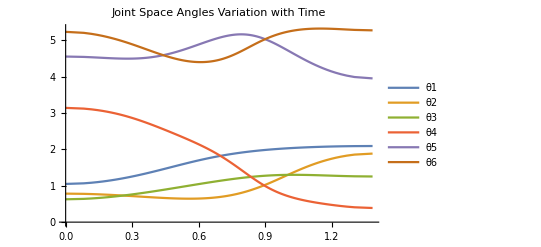

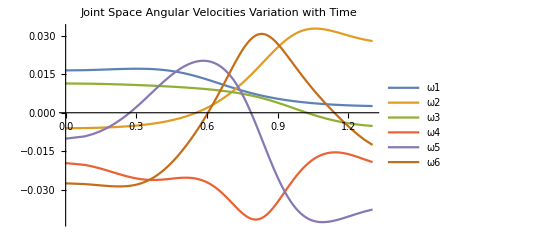

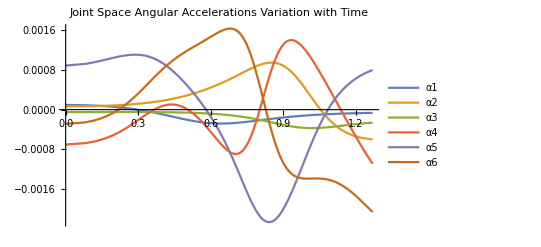

```mathematica
ListLinePlot[{θ1,θ2,θ3,θ4,θ5,θ6},PlotLegends->{"θ1","θ2","θ3","θ4","θ5","θ6"},PlotLabel->"Joint Space Angles Variation with Time"]
ListLinePlot[{ω1,ω2,ω3,ω4,ω5,ω6},PlotLegends->{"ω1","ω2","ω3","ω4","ω5","ω6"},PlotLabel->"Joint Space Angular Velocities Variation with Time"]
ListLinePlot[{α1,α2,α3,α4,α5,α6},PlotLegends->{"α1","α2","α3","α4","α5","α6"},PlotLabel->"Joint Space Angular Accelerations Variation with Time"]
```

### Initializing PUMA 560 Parameters:

```mathematica
dhTab = {{0,0,0,θ1[t]},{0,-π/2,0,θ2[t]},{a2,0,d3,θ3[t]},{a3,-π/2,d4,θ4[t]},{0,π/2,0,θ5[t]},{0,-π/2,0,θ6[t]}};
IList = {{{I11,0,0},{0,I12,0},{0,0,I13}},{{I21,0,0},{0,I22,0},{0,0,I23}},{{I31,0,0},{0,I32,0},{0,0,I33}},{{I41,0,0},{0,I42,0},{0,0,I43}},{{I51,0,0},{0,I52,0},{0,0,I53}},{{I61,0,0},{0,I62,0},{0,0,I63}}};
mList = {m1,m2,m3,m4,m5,m6};
comList = {{comx1,comy1,comz1,1},{comx2,comy2,comz2,1},{comx3,comy3,comz3,1},{comx4,comy4,comz4,1},{comx5,comy5,comz5,1},{comx6,comy6,comz6,1}};
q = {θ1[t],θ2[t],θ3[t],θ4[t],θ5[t],θ6[t]};
```

### Computation of M, C and G:

M is computed by using the fact that it is the sum of the value of mass*LinearJacobianTranspose*LinearJacobian + omegaJacobianTranspose*LinkComMomentOfInertia*omegaJacobian for each link. V is computed by obtaining the transformation matrix for PUMA560 using modules written in previous modules and computing the y-coordinates after which for each link the contribution to potential energy is the product of its mass and acceleration due to gravity and its y-coordinate. The derivative of the potential with respect to the joint variables gives the G Matrix and the C Matrix is obtained from the M matrix by using the module written in question 3 of this assignment.

```mathematica
M = ConstantArray[0,{6,6}];
V = 0;
For[i=1,i<=6,i++,
T = DHTable2HomTrans[dhTab[[1;;i]]];
V += mList[[i]]*g*(T.comList[[i]])[[2]];
Jv = linearVelocityJacobianMatrix[(T.comList[[i]])[[1;;3]],q];
Jw = omegaJacobianBodyFixed[T[[1;;3,1;;3]],q];
M += mList[[i]].Transpose[Jv].Jv+Transpose[Jw].IList[[i]].Jw;
]
CMat = massToCoriolis[M,q,t];
G =  D[V,{q}];
```

### Evaluating M Q̈ + C Q̇ + G with time:

```mathematica
lhsList = ConstantArray[0,{n-1,2}];
For[count=1,count<n,count++,
Print[count];
tempM = M/.{{θ1[t],θ2[t],θ3[t],θ4[t],θ5[t],θ6[t],θ1'[t],θ2'[t],θ3'[t],θ4'[t],θ5'[t],θ6'[t],θ1''[t],θ2''[t],θ3''[t],θ4''[t],θ5''[t],θ6''[t],t}->{θ1[[count,2]],θ2[[count,2]],θ3[[count,2]],θ4[[count,2]],θ5[[count,2]],θ6[[count,2]],ω1[[count,2]],ω2[[count,2]],ω3[[count,2]],ω4[[count,2]],ω5[[count,2]],ω6[[count,2]],α1[[count,2]],α2[[count,2]],α3[[count,2]],α4[[count,2]],α5[[count,2]],α6[[count,2]], ω1[[count,1]]}};
tempC = CMat/.{{θ1[t],θ2[t],θ3[t],θ4[t],θ5[t],θ6[t],θ1'[t],θ2'[t],θ3'[t],θ4'[t],θ5'[t],θ6'[t],θ1''[t],θ2''[t],θ3''[t],θ4''[t],θ5''[t],θ6''[t],t}->{θ1[[count,2]],θ2[[count,2]],θ3[[count,2]],θ4[[count,2]],θ5[[count,2]],θ6[[count,2]],ω1[[count,2]],ω2[[count,2]],ω3[[count,2]],ω4[[count,2]],ω5[[count,2]],ω6[[count,2]],α1[[count,2]],α2[[count,2]],α3[[count,2]],α4[[count,2]],α5[[count,2]],α6[[count,2]], ω1[[count,1]]}};
tempG = G/.{{θ1[t],θ2[t],θ3[t],θ4[t],θ5[t],θ6[t],θ1'[t],θ2'[t],θ3'[t],θ4'[t],θ5'[t],θ6'[t],θ1''[t],θ2''[t],θ3''[t],θ4''[t],θ5''[t],θ6''[t],t}->{θ1[[count,2]],θ2[[count,2]],θ3[[count,2]],θ4[[count,2]],θ5[[count,2]],θ6[[count,2]],ω1[[count,2]],ω2[[count,2]],ω3[[count,2]],ω4[[count,2]],ω5[[count,2]],ω6[[count,2]],α1[[count,2]],α2[[count,2]],α3[[count,2]],α4[[count,2]],α5[[count,2]],α6[[count,2]], ω1[[count,1]]}};
lhsList[[count,1]] = ω1[[count,1]];
lhsList[[count,2]] = tempG+tempC.Transpose[{{ω1[[count,2]],ω2[[count,2]],ω3[[count,2]],ω4[[count,2]],ω5[[count,2]],ω6[[count,2]]}}]+tempM.Transpose[{{α1[[count,2]],α2[[count,2]],α3[[count,2]],α4[[count,2]],α5[[count,2]],α6[[count,2]]}}];
];
```

1

2

3

4

$Aborted

### Plotting M Q̈ + C Q̇ + G with time:

```mathematica
ListLinePlot[{lhsList},PlotLegends->{"M Q̈ + C Q̇ + G"},PlotLabel->"Variation of M Q̈ + C Q̇ + G with Time"]
```

### The code has been completely written but Mathematica is too slow on my system to substitute all the values for the hundreds of points in the huge matrices and evaluate.